# Genetic paths to evolutionary rescue and the distribution of fitness effects along them

## Matthew Osmond, Guillaume Martin, Sarah Otto

mmosmond@gmail.com

## Dependencies

### Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
imagedir="../IMAGES/";(*directory to save figures in*)
datadir="../SOM/SIM_DATA/";(*directory with simulation data*)
```

### Plot styles

```mathematica
labelstyle=Directive[12,FontFamily->"Helvetica"];
defaultcolors=ColorData[1,"ColorList"];
```

### Functions (derived below)

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s]
fm[m_,mwt_,mmax_,λ_,n_]:=Simplify[fs[s,so,λ,n]/.s->m-mwt/.so->mmax-mwt,{mmax>m,λ>0}]

prescue=1-(1-p0)^N0;
prescueApp=1-ⅇ^(-N0 p0);

pest[m_]:=(1-Exp[-2m])HeavisideTheta[m]

prescuem[m_,Λ_]:=1-ⅇ^((1-√(1+(2 Λ)/Abs[m]^2)) Abs[m])

Λ1[m0_?NumericQ,mmax_,λ_,n_,U_]:=U NIntegrate[fm[m,m0,mmax,λ,n]pest[m],{m,0,mmax}]
PR1[m0_?NumericQ]:=prescue/.p0->prescuem[m0,Λ1[m0,mmax,λ,n,U]]
PR1App[m0_?NumericQ]:=prescueApp/.p0->prescuem[m0,Λ1[m0,mmax,λ,n,U]]

fψ=(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ))/(2 √π);
AnciauxEqnA12=U (1-ψwt/2)^(1/2-θ)/(1-ψwt/4)(Exp[-α]/(√(π α))-Erfc[√α]);

Λ2[m0_?NumericQ,mmax_,λ_,n_,U_]:=U NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],{m,-∞,mmax}]

Λ0approx=(2 U √(mmax λ))/(√π);
smallψapproxRescue=-(ⅇ^(-(mmax (1-√(1-mwt/mmax))^2)/λ) (1-mwt/mmax)^((1-n)/2) U Log[(1-√(1+(√(U √(mmax λ)))/(mmax π^(1/4))))/(1-√(1-mwt/mmax))])/((1+1/2 (-1+√(1-mwt/mmax))) π);
verylargeρapproxRescue=-(2 ⅇ^(-(mmax (1-√(1-mwt/mmax))^2)/(2 λ)) (1-mwt/mmax)^((1-n)/2) √(2/π) U)/((1-√(1-mwt/mmax))^3 (1+1/2 (-1+√(1-mwt/mmax))) (mmax/λ)^(3/2));
smallψapproxRescueSuper=(ⅇ^(-(mmax (1-√(1-mwt/mmax))^2)/λ) (1-mwt/mmax)^((1-n)/2) U Log[1/(√2 √(mmax/λ) (1-√(1-(√(U √(mmax λ)))/(mmax π^(1/4)))))])/((1+1/2 (-1+√(1-mwt/mmax))) π);
g1m=(U fm[m,mwt,mmax,λ,n]pest[m])/Λ1[mwt,mmax,λ,n,U];
g1mApp=(ⅇ^(α-1/4 ρmax (ψ-ψwt)^2) √(α ρmax) ψ)/(√(1-m/mmax) mmax ψwt (-1+ⅇ^α √π √α Erfc[√α]));
g2numerator[m0_,m2_?NumericQ]:=U NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,U fm[m2,m,mmax,λ,n]pest[m2]],{m,-∞,mmax}];
g2denominator[m0_?NumericQ]:=NIntegrate[U fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,U fm[m2,m,mmax,λ,n]pest[m2]],{m,-∞,mmax},{m2,0,mmax}];
```

## Example simulations

### 1-step rescue (figure 1)

#### Population size dynamics

Total population size for many replicates

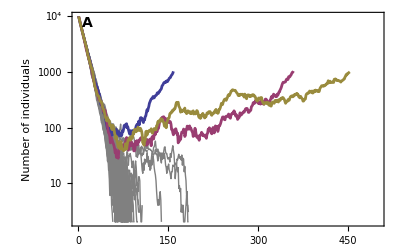

```mathematica
n0="10000";
n="4";
U="0.000100";
Es="0.01000";
mmax="0.50";
mwt="-0.10";
mutmax="2";
nreps=100;

data=Table[
Import[datadir<>"alleles_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>ToString[rep]<>".csv"][[All,1]],
{rep,1,nreps}
];

rescued=Select[data,#[[-1]]>1000&];
extinct=Select[data,#[[-1]]<1000&];

genmax=500;
nmax=n0;

Show[
ListLogPlot[
extinct,
Joined->True,
PlotRange->{{0,genmax},{1,nmax}},
Frame->{True,True,False,False},
FrameLabel->{"","Number of individuals"},
PlotStyle->Gray,LabelStyle->labelstyle,
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->Text[Style["A",14,Bold],Scaled@{0.05,0.95}]
],
ListLogPlot[
rescued,
Joined->True,
PlotStyle->Thickness[0.005]
],
PlotRange->{{0,genmax},Log@{2,10^4}}
]
(*Export[imagedir<>"Vshape.pdf",%];*)

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,nreps,genmax,nmax]
```

#### Mutation dynamics

example of allele dynamics for one rescued replicate

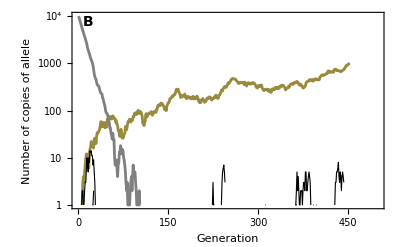

```mathematica
n0="10000";
n="4";
U="0.000100";
Es="0.01000";
mmax="0.50";
mwt="-0.10";
mutmax="2";
rep="83";

genmax=500;
nmax=1000;

Import[datadir<>"alleles_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
alleles=Transpose[PadRight[%]];

Import[datadir<>"kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
allmuts=Transpose[PadRight[%]];

rescuemut=Ordering[alleles[[2;;]][[All,-1]],-1];

Show[
ListLogPlot[
alleles[[2;;]][[rescuemut]],
Joined->True,
PlotRange->{{0,genmax},{1,10^4}},
Frame->{True,True,False,False},
FrameLabel->{"Generation","Number of copies of allele"},
LabelStyle->labelstyle,
Epilog->Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
PlotStyle->Directive[Thickness[0.005],defaultcolors[[3]]]
],
ListLogPlot[
Drop[alleles[[2;;]],rescuemut],
Joined->True,
PlotStyle->Directive[Thickness[0.002],Black]
],
ListLogPlot[
allmuts[[1]],
Joined->True,
PlotStyle->{Gray,Thickness[0.005]}
]
]
(*Export[imagedir<>"VshapeMutations.pdf",%];*)

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,rep,genmax,nmax]
```

### 2-step rescue (figure 2)

#### Population size dynamics

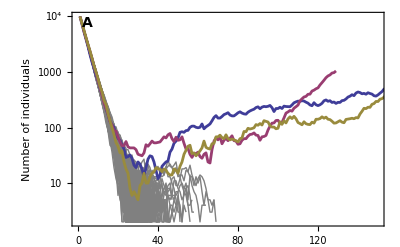

```mathematica
n0="10000";
n="4";
U="0.010000";
Es="0.01000";
mmax="0.50";
mwt="-0.30";
mutmax="2";
intrep=500;
endrep=1000;
nrescued=1000;

data=Table[
Import[datadir<>"alleles_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>ToString[rep]<>".csv"][[All,1]],
{rep,intrep,endrep}
];

rescued=Select[data,#[[-1]]>1000&];
extinct=Select[data,#[[-1]]<1000&];

genmax=150;
nmax=n0;

Show[
ListLogPlot[
extinct,
Joined->True,
PlotRange->{{0,genmax},{1,nmax}},
Frame->{True,True,False,False},
FrameLabel->{"","Number of individuals"},
PlotStyle->Gray,
LabelStyle->labelstyle,
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->Text[Style["A",14,Bold],Scaled@{0.05,0.95}]],
ListLogPlot[rescued,Joined->True,PlotStyle->Thickness[0.005]
],
PlotRange->{{0,genmax},Log@{2,10^4}}
]
(*Export[imagedir<>"Ushape.pdf",%];*)

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,nreps,genmax,nmax,nrescued]
```

#### Mutation dynamics

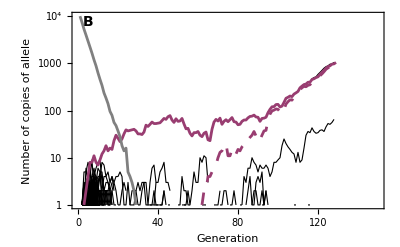

```mathematica
n0="10000";
n="4";
U="0.010000";
Es="0.01000";
mmax="0.50";
mwt="-0.30";
mutmax="2";
rep="675";

genmax=150;
nmax=1000;
ymax=10^4;

Import[datadir<>"alleles_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
alleles=Transpose[PadRight[%]];

Import[datadir<>"kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
allmuts=Transpose[PadRight[%]];

rescuemuts=Ordering[alleles[[2;;]][[All,-1]],-2];

Show[
ListLogPlot[Drop[alleles[[2;;]],{rescuemuts[[1]]},{rescuemuts[[2]]}],Joined->True,PlotStyle->Directive[Black,Thickness[0.002]],
PlotRange->{{0,genmax},{1,ymax}},
Frame->{True,True,False,False},
FrameLabel->{"Generation","Number of copies of allele"},
LabelStyle->labelstyle,
Epilog->Text[Style["B",14,Bold],Scaled@{0.05,0.95}]
],
ListLogPlot[
alleles[[2;;]][[rescuemuts]],
Joined->True,
PlotStyle->{Directive[Thickness[0.005],defaultcolors[[2]],Dashing[Medium]],Directive[Thickness[0.005],defaultcolors[[2]]]}
],
ListLogPlot[allmuts[[1]],Joined->True,PlotStyle->{Gray,Thickness[0.005]}]
]
(*Export[imagedir<>"UshapeMutations.pdf",%];*)

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,rep,genmax,nmax,ymax]
```

Note that the first mutation is subcritical, but the second mutation makes the double mutant supercritical (we can see this because we keep track of what is supercritical in the sims):

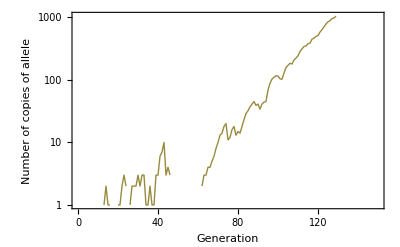

```mathematica
n0="10000";
n="4";
U="0.010000";
Es="0.01000";
mmax="0.50";
mwt="-0.30";
mutmax="2";
rep="675";

genmax=150;
nmax=1000;
ymax=10^4;

Import[datadir<>"supercrit_kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
supermuts=Transpose[PadRight[%]];

ListLogPlot[supermuts,Joined->True,PlotRange->{{0,genmax},{0,nmax}},Frame->{True,True,False,False},FrameLabel->{"Generation","Number of copies of allele"},LabelStyle->labelstyle]

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,rep,genmax,nmax,ymax]
```

The blue replicate is also 2-step rescue

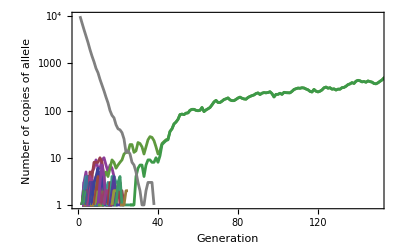

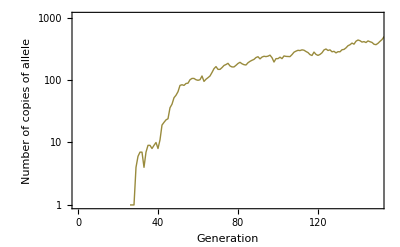

```mathematica
n0="10000";
n="4";
U="0.010000";
Es="0.01000";
mmax="0.50";
mwt="-0.30";
mutmax="2";
rep="629";

genmax=150;
nmax=1000;
ymax=10^4;

Import[datadir<>"alleles_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
alleles=Transpose[PadRight[%]];

Import[datadir<>"kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
allmuts=Transpose[PadRight[%]];

Show[
ListLogPlot[alleles[[2;;]],Joined->True,PlotRange->{{0,genmax},{1,ymax}},Frame->{True,True,False,False},FrameLabel->{"Generation","Number of copies of allele"},LabelStyle->labelstyle,(*Epilog->Text[Style["B",14,Bold],Scaled@{0.05,0.95}],*)
PlotStyle->Thickness[0.005]
],
ListLogPlot[allmuts[[1]],Joined->True,PlotStyle->{Gray,Thickness[0.005]}]
]

Import[datadir<>"supercrit_kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
supermuts=Transpose[PadRight[%]];

ListLogPlot[supermuts,Joined->True,PlotRange->{{0,genmax},{0,nmax}},Frame->{True,True,False,False},FrameLabel->{"Generation","Number of copies of allele"},LabelStyle->labelstyle]

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,rep,genmax,nmax,ymax]
```

but the yellow replicate is 1-step

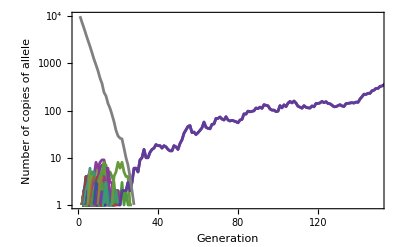

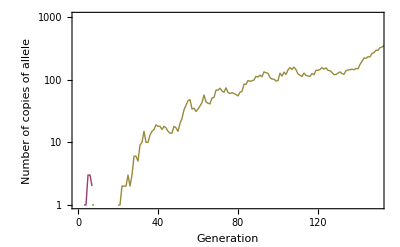

```mathematica
n0="10000";
n="4";
U="0.010000";
Es="0.01000";
mmax="0.50";
mwt="-0.30";
mutmax="2";
rep="752";

genmax=150;
nmax=1000;
ymax=10^4;

Import[datadir<>"alleles_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
alleles=Transpose[PadRight[%]];

Import[datadir<>"kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
allmuts=Transpose[PadRight[%]];

Show[
ListLogPlot[alleles[[2;;]],Joined->True,PlotRange->{{0,genmax},{1,ymax}},Frame->{True,True,False,False},FrameLabel->{"Generation","Number of copies of allele"},LabelStyle->labelstyle,(*Epilog->Text[Style["B",14,Bold],Scaled@{0.05,0.95}],*)
PlotStyle->Thickness[0.005]
],
ListLogPlot[allmuts[[1]],Joined->True,PlotStyle->{Gray,Thickness[0.005]}]
]

Import[datadir<>"supercrit_kmuts_N"<>n0<>"_n"<>n<>"_U"<>U<>"_Es"<>Es<>"_mmax"<>mmax<>"_mwt"<>mwt<>"_mutmax"<>mutmax<>"_rep"<>rep<>".csv"];
supermuts=Transpose[PadRight[%]];

ListLogPlot[supermuts,Joined->True,PlotRange->{{0,genmax},{0,nmax}},Frame->{True,True,False,False},FrameLabel->{"Generation","Number of copies of allele"},LabelStyle->labelstyle]

Clear[n0,n,U,Es,mmax,mwt,r,mutmax,rep,genmax,nmax,ymax]
```

## General

### Distribution of mutant growth rates (equation 1)

In FGM, the PDF of selective effects of new mutations, s = m-m_wt, is (Martin & Lenormand 2015 Evolution)

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
```

where so = m_max-m_wt is the selection coefficient of the optimum phenotype, λ is the mutational variance per trait, and n is the number of traits under selection.

We can translate this into the PDF of mutant growth rates (see also Anciaux et al 2018 Genetics)

```mathematica
fm[m_,mwt_,mmax_,λ_,n_]:=Simplify[fs[s,so,λ,n]/.s->m-mwt/.so->mmax-mwt,{mmax>m,λ>0}]
```

Simulate some mutants

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)

Idn=IdentityMatrix[n];(*matrix to make variance multidimensional*)
NT=10^5;(*number of mutants to create*)
dz=RandomReal[MultinormalDistribution[uo,λ Idn],NT];

Clear[λ,n,Es,η,uo,Idn,NT]
```

Calculate selection coefficient given mutant vectors dz and vector to optimum zopt

```mathematica
ss[dz_,zopt_]:=Table[dz[[i]].zopt-(dz[[i]].dz[[i]])/2,{i,1,Length[dz]}];
```

Check distributions with simulated mutants:

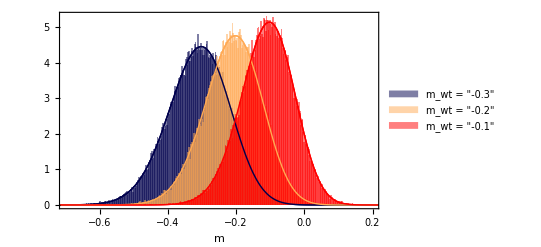

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance per trait*)

mmax=0.5; (*max growth rate*)
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*scaled*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
styl={FontFamily-> "Times",FontSize->10};(*styles of axes and legend*)

legends=Table[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],{i,nmwts}]; simuls=Histogram[Table[mwts[[i]]+ss[dz,zis[[i]]],{i,nmwts}],500,"PDF",ChartStyle->color,PlotRange->{{-2,0.5},All},Axes->False,ChartLegends->Placed[legends,{0.2,0.8}]]; (*simulation results*)

Table[fm[m,mwts[[i]],mmax,λ,n],{i,nmwts}];
theory=Plot[%,{m,-1,0.5},PlotRange->{{-0.7,0.2},All},PlotStyle->color,Frame->{True,True,False,False},FrameLabel->{"m"}];

Show[{theory,simuls,theory},LabelStyle->styl,AxesLabel->{,"f(m | m_wt)"}]
(*Export[imagedir<>"fmmwt.pdf",%];*)

Clear[λ,n,η,Es,mmax,mwts,nmwts,zis,color,styl,legends,simuls,theory]
```

### Probability of rescue (equations 2 and 3)

Let p0 be the probability a wildtype individual has descendants that rescue the population. If we start with N0 wildtypes the probability of rescue is then

```mathematica
prescue=1-(1-p0)^N0;
```

which with small p0 and large N0 is approximately

```mathematica
prescueApp=Series[1-(1-p0)^N0/.p0->p0 ϵ/.N0->N0 /ϵ,{ϵ,0,0}]//Normal
```

1-ⅇ^(-N0 p0)

Let there be X[t,m] individuals in a lineage time t after it arose, given growth rate m. Then the total number of individuals in the lineage is (∫_0)^τ X[t,m] dt  , where τ is the time of extinction. The distribution of the random variable Y[m] = (∫_0)^τ X[t,m] dt is known (see Martin et al 2013 Phil Trans B sup mat); its MGF is

```mathematica
MomentGeneratingFunction[InverseGaussianDistribution[Abs[1/m],1],z]
```

ⅇ^((1-√(1-(2 z)/Abs[m]^2)) Abs[m])

Let an individual with growth rate m produce rescue mutants at rate Λ(m). The probability its lineage rescues the population is then 1-𝔼_Y[ⅇ^(-Y(m)Λ(m))] = 1-M_Y[-Λ(m)] where M_Yis the MGF of Y. Thus evaluating our MGF above at z=-Λ(m) we have the probability of rescue from a genotype with growth rate m

```mathematica
prescuem[m_,Λ_]:=1-MomentGeneratingFunction[InverseGaussianDistribution[Abs[1/m],1],-Λ]
```

### Probability of establishment (equation A1)

Using the Feller diffusion approximation (see Martin et al 2013 Phil Trans B sup mat for details), the probability a mutant establishes is

```mathematica
1-Exp[-2r/σ]
```

1-ⅇ^(-(2 r)/σ)

where r is the infinitesimal mean and σ is the infinitesimal variance in mutant growth rate.

In our discrete generation Poisson process, r is

```mathematica
Expectation[X-1,X\[Distributed]PoissonDistribution[Exp[m]]]
```

-1+ⅇ^m

and σ is

```mathematica
Expectation[(X-1)^2,X\[Distributed]PoissonDistribution[Exp[m]]]-Expectation[X-1,X\[Distributed]PoissonDistribution[Exp[m]]]^2//Simplify//Simplify
```

ⅇ^m

When m is small these are roughly

```mathematica
Series[Exp[m]-1,{m,0,1}]//Normal
```

m

and

```mathematica
Series[Exp[m],{m,0,0}]//Normal
```

1

Then the probability of establishment for m>0 is roughly

```mathematica
1-Exp[-2r/σ]/.r->m/.σ->1
```

and this is zero when m<0.

Note that this reduces to both Haldane’s (1927 Mathematical Proceedings of the Cambridge Philosophical Society) constant population size result and Otto & Whitlock’s (1997 Genetics) changing population size result when m is small

```mathematica
Normal[Series[1-Exp[-2m],{m,0,1}]]/.m->Subscript[m, wt]+s/.Subscript[m, wt]->0
```

2 s

```mathematica
Normal[Series[1-Exp[-2m],{m,0,1}]]/.m->Subscript[m, wt]+s
```

2 (s+m_wt)

### Mutant lineage dynamics

#### Probability generating function

Here we use a continuous time birth (λ) death (μ) process to approximate the dynamics of our discrete time Poisson process (nonoverlapping generations with expected offspring exp(m)). To align these two approaches we need m = λ - μ and, as discussed in Uecker & Hermisson 2016 Genetics and Uecker et al 2014 Am Nat, λ + μ = 1. The latter requirement ensures both processes have the same amount of drift. We follow these studies in equally distributing m between λ and μ, such that λ = (1 + m)/2 and μ = (1 - m)/2. Note that this is only valid for |m|<1.

For a continuous-time birth death process starting from N0 individuals (F[s,0]==s^N0) the PGF for the number of individuals at time t can be solved for explicitly

```mathematica
fst=DSolve[{D[F[s,t],t]==D[F[s,t],s](λ s^2-(λ+μ)s+μ),F[s,0]==s^N0},F[s,t],{s,t}]//Flatten
```

{F[s,t]→((ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) μ)/(ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) λ))^N0}

#### Probability of persistence

The probability of extinction at time t can be obtained from the PGF

```mathematica
pextt=F[s,t]/.fst/.s->0//Factor//FullSimplify
```

(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

Evaluating at s=0 as t goes to infinity gives the probabilty the lineage ever goes extinct. When birth rate is greater than death rate, λ>μ ie m>0, we have

```mathematica
pextinction=Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ>μ,μ>0}]
1-%/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1;
Series[%,{m,0,1}]
```

(μ/λ)^N0

2 m+O[m]^2

(giving Haldane’s classic 2m approximation for the probability of establishment)

and when death rate is greater than birth rate we have

```mathematica
Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ<μ,μ>0}]
```

1

The probability of persistence to time t is just one minus the probability of extinction by time t

```mathematica
pest=1-pextt
```

1-(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

#### Distribution of extinction times (equation A4)

When |m| << 1/t << 1, ie |1/m| >> t >> 1 (that is, at late times but while the mutant is still effectively critical) the probability that a new mutant persists to time t is approximately

```mathematica
pestapp1=Normal[Series[pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1/.m ->m ϵ^2/.t->t /ϵ,{ϵ,0,1}]]/.ϵ->1
```

2/t

And when -m t >>1, ie -m >> 1/t (that is, when the mutant is effectively subcritical) we have roughly

```mathematica
pestapp2=Simplify[pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1]/. 1+ⅇ^(-m t) (-1+m)+m->ⅇ^(-m t) (-1+m)/.-1+m->-1
```

-2 ⅇ^(m t) m

Visually check the critical (red) and subcritical (green) approximations of the true solution (blue)

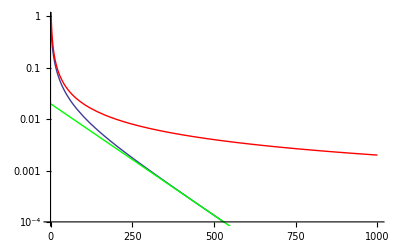

```mathematica
Show[
LogPlot[pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1/.m->-0.01,{t,0,1000},PlotRange->{10^-4,1}],
LogPlot[pestapp1/.m->-0.01,{t,0,1000},PlotRange->All,PlotStyle->Red],
LogPlot[pestapp2/.m->-0.01,{t,0,1000},PlotRange->All,PlotStyle->Green]
]
```

Our equations for persistence times line-up with Weissman et al 2010 Genetics eq A2, but with an additional factor of 2 because we have b+d=2 while they have b+d=1. They point out that the distribution of persistence time has a long tail (like 1/t) before falling off exponentially when t > -1 / m (as can be seen in the plot above). Thus we can essentially say that a mutant lineage will not persist past t = -1 / m.

#### Distribution of lineage sizes

The probability that there is 1 individual at time t is

```mathematica
pn1=D[F[s,t]/.fst,{s,n}]/n!/.n->1/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

(4 ⅇ^(m t) m^2)/((-1+m+ⅇ^(m t) (1+m))^2)

and two individuals

```mathematica
pn2=D[F[s,t]/.fst,{s,n}]/n!/.n->2/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

(4 ⅇ^(m t) (-1+ⅇ^(m t)) m^2 (1+m))/((-1+m+ⅇ^(m t) (1+m))^3)

three

```mathematica
D[F[s,t]/.fst,{s,n}]/n!/.n->3/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

(4 ⅇ^(m t) (-1+ⅇ^(m t))^2 m^2 (1+m)^2)/((-1+m+ⅇ^(m t) (1+m))^4)

From this series we can see that we can write the probability of n individuals at time t like

```mathematica
pnt=pn1(pn2/pn1)^(n-1)
```

(4 ⅇ^(m t) m^2 (((-1+ⅇ^(m t)) (1+m))/(-1+m+ⅇ^(m t) (1+m)))^(-1+n))/((-1+m+ⅇ^(m t) (1+m))^2)

Check for n=4:

```mathematica
pnt/(D[F[s,t]/.fst,{s,n}]/n!)/.n->4/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

1

#### Distribution of lineage sizes given persistence (equation A5)

Dividing the probability of having n individuals at time t by the probability of survival to time t gives the conditional probability of having n individuals at time t given a mutant lineage lives to time t

```mathematica
pntgt=pnt/pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//FullSimplify
```

(2 m (1-(2 m)/(-1+m+ⅇ^(m t) (1+m)))^n)/((-1+ⅇ^(m t)) (1+m))

When t << |1/m|  (effectively critical) this is approximately

```mathematica
pntgtapp1=Normal[Series[pntgt/.m-> m ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
Simplify[%==2 (1/t)(1+2/t)^-n,{t>0,n>0}]
```

2 t^(-1+n) (2+t)^-n

True

with expectation

```mathematica
Sum[n pntgtapp1,{n,0,∞}]
```

(2+t)/2

Using this expectation, the cumulative number of individuals over T generations is roughly

```mathematica
Sum[t/2,{t,0,T}]
```

1/4 T (1+T)

Or when -1/m << t (ie subcritical mutants) we have approximately

```mathematica
pntgtapp2=pntgt/.-1+m+ⅇ^(m t) (1+m)->-1+m/.-1+ⅇ^(m t)->-1//Simplify;
%/. 1-m->1
```

-2 m (1+m)^(-1+n)

with expectation

```mathematica
Sum[n pntgtapp2,{n,0,∞}]
```

(-1+m)/(2 m)

Visually check critical (red) and subcritical (green) approximations against true solution (blue) for n=20 across time

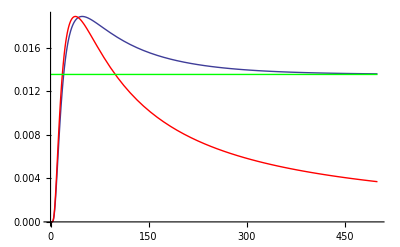

```mathematica
Show[
Plot[pntgt/.m->-0.01/.n->20,{t,0,500},PlotRange->All],
Plot[pntgtapp1/.m->-0.01/.n->20,{t,0,500},PlotRange->All,PlotStyle->Red],
Plot[pntgtapp2/.m->-0.01/.n->20,{t,0,500},PlotRange->All,PlotStyle->Green]
]
```

Check distribution of n at 3 different times

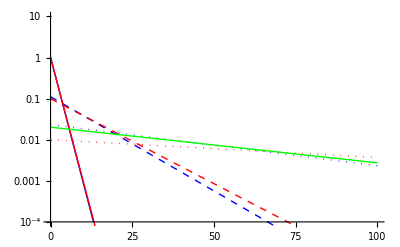

```mathematica
nmax=100;
Show[
LogPlot[pntgt/.m->-0.01/.t->2,{n,0,nmax},PlotStyle->Blue,PlotRange->{10^-4,10}],
LogPlot[pntgt/.m->-0.01/.t->20,{n,0,nmax},PlotStyle->{Blue,Dashed},PlotRange->All],
LogPlot[pntgt/.m->-0.01/.t->200,{n,0,nmax},PlotStyle->{Blue,Dotted,Thick},PlotRange->All],
LogPlot[pntgtapp1/.m->-0.01/.t->2,{n,0,nmax},PlotRange->All,PlotStyle->Red],
LogPlot[pntgtapp1/.m->-0.01/.t->20,{n,0,nmax},PlotRange->All,PlotStyle->{Red,Dashed}],
LogPlot[pntgtapp1/.m->-0.01/.t->200,{n,0,nmax},PlotRange->All,PlotStyle->{Red,Dotted,Thick}],
LogPlot[pntgtapp2/.m->-0.01,{n,0,nmax},PlotRange->All,PlotStyle->Green]
]
```

These lineage sizes given persistence align with eq A3 in Weissman et al 2010. As they pointed out, the distribution of n given persistence to t and m is roughly geometric in both cases (t<<|1/m| and t>>-1/m), with p=1/t or p=-m respectively, which implies that the probability of n drops off exponentially when n>min(t, -1/m). Thus n will essentially never be greater than the minimum of t or -1/m, eg mutants with large -m will be restricted to small sizes.

## Probability of rescue

### 1-step rescue (equation 4)

The probability that a mutant with growth rate in [m,m+dm] rescues the popuation is f[m|m_wt] p_est[m] dm. Integrating over all m>0 gives the probability of 1-step rescue from an individual with growth rate m0

```mathematica
Clear[Λ1]
```

```mathematica
Λ1[m0_?NumericQ,mmax_,λ_,n_,U_]:=U NIntegrate[fm[m,m0,mmax,λ,n]pest[m],{m,0,mmax}]
```

The total probability of 1-step rescue is then

```mathematica
PR1[m0_?NumericQ]:=prescue/.p0->prescuem[m0,Λ1[m0,mmax,λ,n,U]]
```

And we can approximate this as

```mathematica
PR1App[m0_?NumericQ]:=prescueApp/.p0->prescuem[m0,Λ1[m0,mmax,λ,n,U]]
```

Numerical example

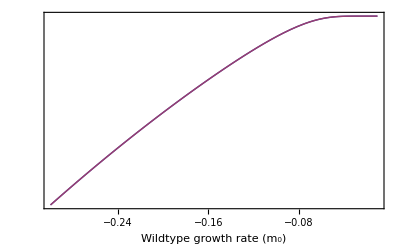

```mathematica
N0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

LogPlot[
{PR1[m0],PR1App[m0]},
{m0,-0.3,-0.01},
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate (m_0)","","","Probability of rescue"},
FrameTicks->{True,False,False,True}
]

Clear[N0,U,mmax,λ,Es,n,mwt]
```

### 2-step rescue (equation 5)

The rate of 2-step rescue from a single individual with growth rate m0 is the probability of a mutation to growth rate m, which does not establish, but then creates a second mutation that does

```mathematica
Λ2[m0_?NumericQ,mmax_,λ_,n_,U_]:=U NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],{m,-∞,mmax}]
```

Numerical comparison with probability of 1-step rescue

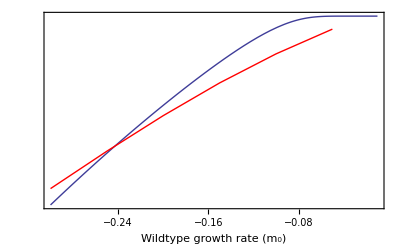

```mathematica
N0=10^4;
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

Table[{m0,prescue/.p0->prescuem[m0,Λ2[m0,mmax,λ,n,U]]},{m0,-0.3,-0.01,0.05}];
plot1=ListLogPlot[%,Joined->True,PlotStyle->Red];

plot2=LogPlot[PR1[m0],{m0,-0.3,-0.01},Frame->{True,False,False,True},FrameLabel->{"Wildtype growth rate (m_0)","","","Probability of rescue"},FrameTicks->{True,False,False,True}];

Show[plot2,plot1]

Clear[mmax,λ,Es,n,N0,U]
```

### k-step rescue (equation 6)

One can carry on the logic used for 2-step rescue to get the probability of k-step rescue, e.g., 3-step is

```mathematica
Λ3[m0_?NumericQ,mmax_,λ_,n_,U_]:=U NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ2[m,mmax,λ,n,U]],{m,-∞,mmax}]
```

and 4-step is

```mathematica
Λ4[m0_?NumericQ,mmax_,λ_,n_,U_]:=U NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ3[m,mmax,λ,n,U]],{m,-∞,mmax}]
```

etc

### Plot probability as a function of wildtype growth rate (figure 3)

The probability of rescue by k steps involves k integrals, and so with even small k (e.g, k=3) they are very slow to compute in their exact form. We can, however, combine an approximation (don’t integrate below mmin) with interpolation functions to greatly speed things up (with some loss of accuaracy)

```mathematica
mTempmin=-0.4;
mTempmax=-0.01;
step=0.01;
mmin=mTempmin;

Clear[Λ1Interpolated,Λ2Interpolated,Λ3Interpolated,Λ4Interpolated]

Λ1Interpolated[m0_,mmax_,λ_,n_,U_]:=Λ1Interpolated[m0,mmax,λ,n,U]=Block[{},
f=Interpolation[Table[{mTemp,U NIntegrate[fm[m,mTemp,mmax,λ,n]pest[m],{m,0,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{mTemp,mTempmin,mTempmax,step}]];
f[m0]
]

Λ2Interpolated[m0_,mmax_,λ_,n_,U_]:=Λ2Interpolated[m0,mmax,λ,n,U]=Block[{},
f=Interpolation[Table[{mTemp,U NIntegrate[fm[m,mTemp,mmax,λ,n](1-pest[m])prescuem[m,Λ1Interpolated[m,mmax,λ,n,U]],{m,mmin,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{mTemp,mTempmin,mTempmax,step}]];
f[m0]
]

Λ3Interpolated[m0_,mmax_,λ_,n_,U_]:=Λ3Interpolated[m0,mmax,λ,n,U]=Block[{},
f=Interpolation[Table[{mTemp,U NIntegrate[fm[m,mTemp,mmax,λ,n](1-pest[m])prescuem[m,Λ2Interpolated[m,mmax,λ,n,U]],{m,mmin,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{mTemp,mTempmin,mTempmax,step}]];
f[m0]
]

Λ4Interpolated[m0_,mmax_,λ_,n_,U_]:=Λ4Interpolated[m0,mmax,λ,n,U]=Block[{},
f=Interpolation[Table[{mTemp,U NIntegrate[fm[m,mTemp,mmax,λ,n](1-pest[m])prescuem[m,Λ3Interpolated[m,mmax,λ,n,U]],{m,mmin,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{mTemp,mTempmin,mTempmax,step}]];
f[m0]
]
```

Use this to plot the probability of rescue as a function of wildtype decline rate

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.43635×10^-7 and 1.03478×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.02467×10^-7 and 1.09211×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.85095×10^-7 and 2.32174×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 5.34505×10^-8 and 5.95153×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 7.05903×10^-8 and 8.58885×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 9.31464×10^-8 and 1.71162×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.43635×10^-7 and 1.03478×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.02467×10^-7 and 1.09211×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.85095×10^-7 and 2.32174×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

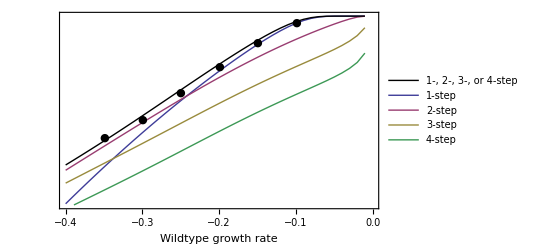

```mathematica
N0=10^4;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
U=2*10^-3;

dat1=Import[datadir<>"prescue_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mutmax10_nreps1000.csv"];
dat2=Import[datadir<>"prescue_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mutmax10_nreps10000.csv"];
dat3=Import[datadir<>"prescue_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mutmax10_nreps100000.csv"];
alldat=Flatten[{dat1,dat2,dat3},{1,2}];

m0min=mTempmin;
m0max=mTempmax;
mstep=step;
rate4=Table[{m0,Λ4Interpolated[m0,mmax,λ,n,U]},{m0,m0min,m0max,mstep}];
rate3=Table[{m0,Λ3Interpolated[m0,mmax,λ,n,U]},{m0,m0min,m0max,mstep}];
rate2=Table[{m0,Λ2Interpolated[m0,mmax,λ,n,U]},{m0,m0min,m0max,mstep}];
rate1=Table[{m0,Λ1Interpolated[m0,mmax,λ,n,U]},{m0,m0min,m0max,mstep}];
m0list=Table[m0,{m0,m0min,m0max,mstep}];
theory={
Table[{m0list[[i]],prescue/.p0->prescuem[m0list[[i]],rate1[[i,2]]]},{i,Length[m0list]}],
Table[{m0list[[i]],prescue/.p0->prescuem[m0list[[i]],rate2[[i,2]]]},{i,Length[m0list]}],
Table[{m0list[[i]],prescue/.p0->prescuem[m0list[[i]],rate3[[i,2]]]},{i,Length[m0list]}],
Table[{m0list[[i]],prescue/.p0->prescuem[m0list[[i]],rate4[[i,2]]]},{i,Length[m0list]}]
};
alltheory=Table[{m0list[[i]],prescue/.p0->prescuem[m0list[[i]],rate1[[i,2]]+rate2[[i,2]]+rate3[[i,2]]+rate4[[i,2]]]},{i,Length[m0list]}];

Show[
ListLogPlot[theory,
Joined->True,
PlotStyle->Thick,
PlotRange->{{m0min,0},{5*10^-7,1}},
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Probability of rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"1-step","2-step","3-step","4-step"}],Scaled@{3/4,1/4}]
],
ListLogPlot[alltheory,Joined->True,PlotStyle->{Black,Thick},
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"1-, 2-, 3-, or 4-step"}],Scaled@{1/4,7/8}]
],
ListLogPlot[alldat,PlotMarkers->{Automatic,Medium},PlotStyle->Black
]
]

(*Export[imagedir<>"4stepNormalU_sims.pdf",%];*)

Clear[N0,mmax,λ,Es,n,U,m0min,m0max]
```

### Plot probability as a function of mutation rate (figure S1)

We again use interpolation functions to speed things up, this time across U instead of m0

```mathematica
Umin=-5;
Umax=1;
Ustep=0.1;
mmin=-0.4;

Clear[Λ1InterpolatedU,Λ2InterpolatedU,Λ3InterpolatedU,Λ4InterpolatedU]

Λ1InterpolatedU[m0_,mmax_,λ_,n_,x_]:=Λ1InterpolatedU[m0,mmax,λ,n,x]=Block[{},
f=Interpolation[Table[{xtemp,10^xtemp NIntegrate[fm[m,m0,mmax,λ,n]pest[m],{m,0,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{xtemp,Umin,Umax,Ustep}]];
f[x]
]

Λ2InterpolatedU[m0_,mmax_,λ_,n_,x_]:=Λ2InterpolatedU[m0,mmax,λ,n,x]=Block[{},
f=Interpolation[Table[{xtemp,10^xtemp NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1Interpolated[m,mmax,λ,n,10^xtemp]],{m,mmin,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{xtemp,Umin,Umax,Ustep}]];
f[x]
]

Λ3InterpolatedU[m0_,mmax_,λ_,n_,x_]:=Λ3InterpolatedU[m0,mmax,λ,n,x]=Block[{},
f=Interpolation[Table[{xtemp,10^xtemp NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ2Interpolated[m,mmax,λ,n,10^xtemp]],{m,mmin,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{xtemp,Umin,Umax,Ustep}]];
f[x]
]

Λ4InterpolatedU[m0_,mmax_,λ_,n_,x_]:=Λ4InterpolatedU[m0,mmax,λ,n,x]=Block[{},
f=Interpolation[Table[{xtemp,10^xtemp NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ3Interpolated[m,mmax,λ,n,10^xtemp]],{m,mmin,mmax},Method->{Automatic,"SymbolicProcessing"->0}]},{xtemp,Umin,Umax,Ustep}]];
f[x]
]
```

with slow decline

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 7.90364×10^-10 and 3.57265×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.13275×10^-9 and 5.95088×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.62463×10^-9 and 9.92946×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 8.75331×10^-9 and 4.7503×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.35755×10^-8 and 7.25858×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.10269×10^-8 and 1.09926×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 9.0895×10^-6 and 2.1133×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 0.0000111964 and 2.23643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 0.0000137845 and 2.3908×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

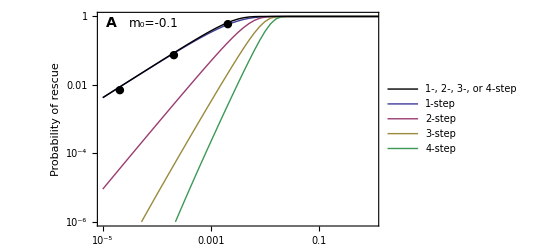

```mathematica
N0=10^4;
m0=-0.1;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

rate4=Table[Λ4InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate3=Table[Λ3InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate2=Table[Λ2InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate1=Table[Λ1InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
Ulist=Table[10^x,{x,Umin,Umax,Ustep}];
theory={
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate1[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate2[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate3[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate4[[i]]]},{i,Length[Ulist]}]
};
alltheory=Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate1[[i]]+rate2[[i]]+rate3[[i]]+rate4[[i]]]},{i,Length[Ulist]}];

dat=Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.10_nreps10000.csv"];
dat[[All,{1}]]=dat[[All,{1}]]*Uc/.Uc->n^2 λ/4/.λ->2Es/n;

Show[
ListLogLogPlot[Re[theory],Joined->True,PlotStyle->Thick,
PlotRange->{{10^-5,1},{10^-6,1}},
Frame->{True,True,False,False},
FrameLabel->{,"Probability of rescue",,},
FrameTicks->{True,True,False,False},
LabelStyle->labelstyle,
Epilog->{Text[Style["A",14,Bold],Scaled@{0.05,0.95}],Text[Style["m_0=-0.1",12,FontFamily->"Helvetica"],Scaled@{2/10,9.5/10}]},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"1-step","2-step","3-step","4-step"}],Scaled@{3/4,2/4}]
],
ListLogLogPlot[Re[alltheory],Joined->True,PlotStyle->{Thick,Black},
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"1-, 2-, 3-, or 4-step"}],Scaled@{3/4,1/8}]
],
ListLogLogPlot[dat,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"4step_lowm0.pdf",%];*)

Clear[mmax,λ,Es,n,m0,N0,U]
```

medium decline

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 7.68995×10^-13 and 3.14585×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.50181×10^-12 and 6.1428×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.92903×10^-12 and 1.19802×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 8.84557×10^-10 and 3.68568×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.37187×10^-9 and 5.63207×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.12528×10^-9 and 8.52985×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 7.95624×10^-7 and 1.85625×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 9.82598×10^-7 and 2.00651×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.21301×10^-6 and 2.195×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

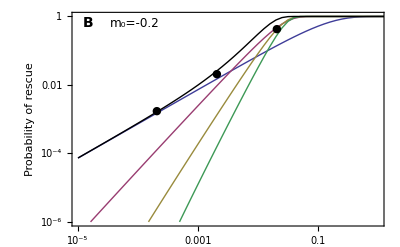

```mathematica
N0=10^4;
m0=-0.2;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

rate4=Table[Λ4InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate3=Table[Λ3InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate2=Table[Λ2InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate1=Table[Λ1InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
Ulist=Table[10^x,{x,Umin,Umax,Ustep}];
theory={
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate1[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate2[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate3[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate4[[i]]]},{i,Length[Ulist]}]
};
alltheory=Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate1[[i]]+rate2[[i]]+rate3[[i]]+rate4[[i]]]},{i,Length[Ulist]}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.20_mutmax10_nreps10000.csv"];
dat[[All,{1}]]=dat[[All,{1}]]*Uc/.Uc->n^2 λ/4/.λ->2Es/n;

Show[
ListLogLogPlot[Re[theory],Joined->True,PlotStyle->Thick,
PlotRange->{{10^-5,1},{10^-6,1}},
Frame->{True,True,False,False},
FrameLabel->{,"Probability of rescue",,},
FrameTicks->{True,True,False,False},
LabelStyle->labelstyle,
Epilog->{Text[Style["B",14,Bold],Scaled@{0.05,0.95}],Text[Style["m_0=-0.2",12,FontFamily->"Helvetica"],Scaled@{2/10,9.5/10}]},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic}
],
ListLogLogPlot[Re[alltheory],Joined->True,PlotStyle->{Thick,Black}],
ListLogLogPlot[dat,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"4step_medm0.pdf",%];*)

Clear[mmax,λ,Es,n,m0,N0,U]
```

fast decline

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 4.48721×10^-14 and 7.45286×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 8.76425×10^-14 and 1.44261×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.70913×10^-13 and 2.79389×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 4.71176×10^-11 and 8.59557×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 7.31131×10^-11 and 1.31351×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 1.13365×10^-10 and 1.98929×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 2.90847×10^-8 and 4.24615×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 3.61726×10^-8 and 4.57071×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.000767263}. NIntegrate obtained 4.498×10^-8 and 4.97733×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

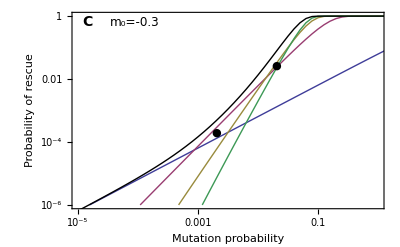

```mathematica
N0=10^4;
m0=-0.3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

rate4=Table[Λ4InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate3=Table[Λ3InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate2=Table[Λ2InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
rate1=Table[Λ1InterpolatedU[m0,mmax,λ,n,x],{x,Umin,Umax,Ustep}];
Ulist=Table[10^x,{x,Umin,Umax,Ustep}];
theory={
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate1[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate2[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate3[[i]]]},{i,Length[Ulist]}],
Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate4[[i]]]},{i,Length[Ulist]}]
};
alltheory=Table[{Ulist[[i]],prescue/.p0->prescuem[m0,rate1[[i]]+rate2[[i]]+rate3[[i]]+rate4[[i]]]},{i,Length[Ulist]}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.30_mutmax10_nreps10000.csv"];
dat[[All,{1}]]=dat[[All,{1}]]*Uc/.Uc->n^2 λ/4/.λ->2Es/n;

Show[
ListLogLogPlot[Re[theory],Joined->True,PlotStyle->Thick,
PlotRange->{{10^-5,1},{10^-6,1}},
Frame->{True,True,False,False},
FrameLabel->{"Mutation probability","Probability of rescue",,},
FrameTicks->{True,True,False,False},
LabelStyle->labelstyle,
Epilog->{Text[Style["C",14,Bold],Scaled@{0.05,0.95}],Text[Style["m_0=-0.3",12,FontFamily->"Helvetica"],Scaled@{2/10,9.5/10}]}
],
ListLogLogPlot[Re[alltheory],Joined->True,PlotStyle->{Thick,Black}],
ListLogLogPlot[dat,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"4step_highm0.pdf",%];*)

Clear[mmax,λ,Es,n,m0,N0,U]
```

## Approximating the probability of 1-step rescue

### Replicating Anciaux et al 2018, Genetics

#### Change of variables

We first introduce the variables y = m/mmax, ywt = mwt/mmax, ρmax = mmax/λ, θ = n/2. The distribution of y among new mutations is then

```mathematica
fy=ⅇ^(-(2-y-ywt) ρmax) ρmax^θ(1-y)^(θ-1) Hypergeometric0F1Regularized[θ,(1-y) (1-ywt) ρmax^2]
Simplify[fy==fm[y mmax,ywt mmax,mmax,mmax/ρmax,2θ]/D[m/mmax,m],{ρmax>0,0<y<1}]
fy/.y->m/mmax/.ywt->mwt/mmax/.ρmax->mmax/λ/.θ->n/2;
Simplify[%D[m/ mmax,m]==fm[m,mwt,mmax,λ,n],{mmax>0,λ>0}]
```

ⅇ^((-2+y+ywt) ρmax) (1-y)^(-1+θ) ρmax^θ Hypergeometric0F1Regularized[θ,(1-y) (1-ywt) ρmax^2]

True

True

#### Approximate hypergeometric function

We next want to approximate the hypergeometric function in fy.

Note first that Hypergeometric0F1Regularized[θ,z] is defined in Mathematica as Hypergeometric0F1[θ,z]/Gamma[θ]:

```mathematica
Hypergeometric0F1Regularized[θ,z];
Hypergeometric0F1[θ,z]/Gamma[θ];
FullSimplify[%/%%]
```

1

Next note that Hypergeometric0F1[θ,z] can be written as Gamma[θ]/(√z)^(θ-1) BesselI[θ-1,2 √z] using 9.6.47 of Abramowitz and Stegun (1964):

```mathematica
Hypergeometric0F1[θ,z];
Gamma[θ]/(√z)^(θ-1) BesselI[θ-1,2 √z];
FullSimplify[%/%%]
```

1

Thus, the Hypergeometric0F1Regularized[θ,z] can be written as 1/(√z)^(θ-1) BesselI[θ-1,2 √z]:

```mathematica
Hypergeometric0F1Regularized[θ,z];
1/(√z)^(θ-1) BesselI[θ-1,2 √z];
FullSimplify[%/%%]
```

1

Finally, 9.7.1 of Abramowitz and Stegun (1964) gives an asymptotic expansion for BesselI that holds for large |z|:

```mathematica
BesselI[θ-1,2 Sqrt[z]]/.BesselI->Function[{v,x},ⅇ^x/(√(2π x))(1-(μ-1)/(8 x)+((μ-1)(μ-9))/(2!(8 x)^2)-((μ-1)(μ-9)(μ-25))/(3!(8 x)^3)+added)/.μ->4 v^2];
```

where the k^th term added to “1” is obtained by taking the previous term and multiplying by -(μ-(2k-1)^2)/(k(8 z)).  For large z, the Bessel function will be dominated by the leading term:

```mathematica
BesselI[θ-1,2 Sqrt[z]]/.BesselI->Function[{v,x},ⅇ^x/(√(2π x))]
```

ⅇ^(2 √z)/(2 √π z^(1/4))

This allows us to conclude that Hypergeometric0F1Regularized[θ,z]=1/(√z)^(θ-1) BesselI[θ-1,2 √z] can be approximated for z large as 1/(√z)^(θ-1) ⅇ^(2 √z)/(2 √π z^(1/4)), which upon rearranging gives    (ⅇ^(2 √z)z^(1/4 (1-2 θ)))/(2 √π).

We can therefore use the following approximation as ρmax = mmax/λ goes to infinity, i.e., mutant growth rates are much less than maximal

```mathematica
fya=FullSimplify[fy/.Hypergeometric0F1Regularized->Function[{θ,z},1/(2 √π)z^((1-2θ)/4)ⅇ^(2 √z)]//PowerExpand,0<y<1&&ρmax>0&&ywt<0&&θ≥1/2]
FullSimplify[%==(ⅇ^(-v[y]) (1-y)^(θ/2-3/4) (1-ywt)^(1/4-θ/2) √ρmax)/(2 √π)/.v[y]->(2-ywt-2 √((1-ywt)(1-y))-y) ρmax,{ρmax>0,ywt<0,0<y<1,θ≥1/2}] (*compare to eqn A9*)
```

-(ⅇ^((-2+y+2 √((-1+y) (-1+ywt))+ywt) ρmax) ((-1+y)/(-1+ywt))^(θ/2) (-1+ywt) √ρmax)/(2 √π ((-1+y) (-1+ywt))^(3/4))

True

This does great for large ρmax, especially at the tails

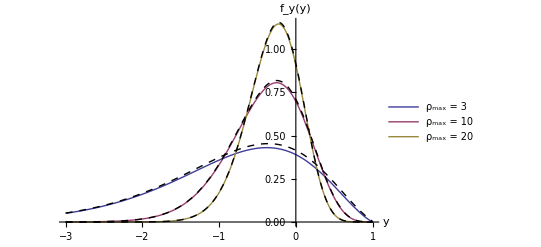

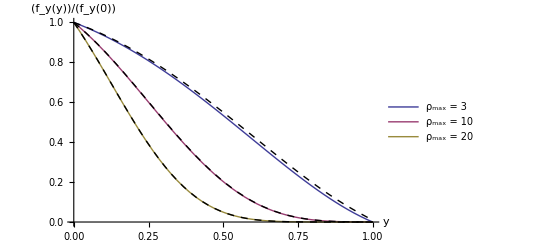

```mathematica
θ=2;ywt=-0.2;ρmax={3,10,20};fy;
Plot[%,{y,-3,1},PlotRange->All, PlotLegends->LineLegend[Table[StringForm["ρ_max = ``",Round[ρmax[[i]]]],{i,Length[ρmax]}]]];
fya;
Plot[%,{y,-3,1},PlotRange->All,PlotStyle->{{Dashed,Black}}];
Show[%%%,%,AxesLabel->{y,Subscript[f, y][y]}]
fy/(fy/.y->0);
Plot[%,{y,0,1},PlotRange->All, PlotLegends->LineLegend[Table[StringForm["ρ_max = ``",Round[ρmax[[i]]]],{i,Length[ρmax]}]]];
fya/(fya/.y->0);
Plot[%,{y,0,1},PlotRange->All,PlotStyle->{{Dashed,Black}}];
Show[%%%,%,AxesLabel->{y,(Subscript[f, y][y])/(Subscript[f, y][0])}]
θ=.;ywt=.;ρmax=.;
```

#### Change of variables

We now consider the variable ψ = 2(1-√(1-y)), which varies between 0 and 2 as y varies between 0 and 1, and is 2 A/B, where A is the phenotypic distance to the closest critical phenotype and B is the distance from a critical phenotype to the optimal

```mathematica
2 (√(1-y)-1)/.y->m/mmax//Expand
FullSimplify[2(Subscript[x, 0]-Subscript[x, c])/Subscript[x, c]==%/.Flatten[Solve[{√(2(mmax-m))==Subscript[x, 0],√(2mmax)==Subscript[x, c]},{mmax,m}]]//Expand,Subscript[x, 0]>0&&Subscript[x, c]>0]
```

-2+2 √(1-m/mmax)

True

The pdf of ψ is then approximately

```mathematica
Solve[{2 (1-√(1-y))==ψ,2 (1-√(1-ywt))==ψwt},{y,ywt}]//Flatten
Simplify[Abs[D[y/.%,ψ]]fya/.%,{0<ψ<2,ψwt<0,ρmax>0,θ≥1/2}]
FullSimplify[%==(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ))/(2 √π),{0<ψ<2,ψwt<0,ρmax>0,θ≥1/2}](*compare to eqn A10*)
fψ=(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ))/(2 √π);
```

{y→1/4 (4 ψ-ψ^2),ywt→1/4 (4 ψwt-ψwt^2)}

-(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) √ρmax ((-2+ψ)/(-2+ψwt))^(1+θ) (-2+ψwt)^3)/(2 √π ((-2+ψ)^2 (-2+ψwt)^2)^(3/4))

True

Note that this is a normal distribution, with mean ψwt and variance 2/ρmax, as ((-2+ψ)/(-2+ψwt))^(-1/2+θ)→ 1 (which is reasonable when the absolute values of ψ and ψwt are much less than 2, i.e., growth rates small relative to max, or when θ is 1/2, i.e., when dimensionality is low).

```mathematica
fψ/. ((2-ψ)/(2-ψwt))^(-1/2+θ)->1;
Simplify[%==Simplify[PDF[NormalDistribution[ψwt,√(2/ρmax)],ψ],ρmax>0],{0<ψ<2,ψwt<0,ρmax>0,θ>1/2}]
```

True

#### Laplace approximation and compact form (equation A2)

Anciaux et al’s equation A5 is the integral of the following over y from 0 to 1

```mathematica
U/-mwt pest[m] fy/.m->mmax y
```

-(ⅇ^((-2+y+ywt) ρmax) (1-ⅇ^(-2 mmax y)) U (1-y)^(-1+θ) ρmax^θ Hypergeometric0F1Regularized[θ,(1-y) (1-ywt) ρmax^2])/mwt

which, using the approximation in equation A9, is nearly

```mathematica
U/-mwt pest[m] fya/.m->mmax y
```

(ⅇ^((-2+y+2 √((-1+y) (-1+ywt))+ywt) ρmax) (1-ⅇ^(-2 mmax y)) U ((-1+y)/(-1+ywt))^(θ/2) (-1+ywt) √ρmax)/(2 mwt √π ((-1+y) (-1+ywt))^(3/4))

which is roughly the integral of the following over ψ from 0 to 2 (A10)

```mathematica
U/-mwt(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ))/(2 √π)
```

Anciuaux et al 2018 say we can write this as (A11)

```mathematica
h[ψ_]:=  ((1-ψ/2)/(1-ψwt/2))^(θ-1/2)(1-ⅇ^(-2 mmax y))/.y->ψ(1-ψ/4)
q[ψ_]:=1/4 (ψ-ψwt)^2
U/-mwt(√ρmax)/(2 √π)h[ψ]Exp[-ρmax q[ψ]]
```

-(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) (1-ⅇ^(-2 mmax (1-ψ/4) ψ)) U √ρmax ((1-ψ/2)/(1-ψwt/2))^(-1/2+θ))/(2 mwt √π)

which appears to be true only when we ignore this second term they have in h (but this will drop out anyway when we take the leading order in the next step)

```mathematica
Simplify[(-(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) (1-ⅇ^(-2 mmax (1-ψ/4) ψ)) U √ρmax ((1-ψ/2)/(1-ψwt/2))^(-1/2+θ))/(2 mwt √π))/(U/-mwt(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ))/(2 √π))]
```

1-ⅇ^(1/2 mmax (-4+ψ) ψ)

As ρmax=mmax/λ goes to ∞ the Exp term dominates and we take the leading order of h

```mathematica
h0=Normal[Series[h[ψ],{ψ,0,1}]]
```

2 mmax ψ (1/(1-ψwt/2))^(-1/2+θ)

Now taking the integral over ψ from 0 to ∞ we get A12

```mathematica
Integrate[U/-mwt(√ρmax)/(2 √π)h0 Exp[-ρmax q[ψ]],{ψ,0,∞},Assumptions->{ρmax>0,ψwt<0}]/.mwt->ψwt(1-ψwt/4)mmax;
FullSimplify[%==U (1-ψwt/2)^(1/2-θ)/(1-ψwt/4)(Exp[-α]/(√(π α))-Erfc[√α])/.α->(ρmax ψwt^2)/4,{ψwt<0,ρmax>0,U>0}]
```

True

```mathematica
AnciauxEqnA12=U (1-ψwt/2)^(1/2-θ)/(1-ψwt/4)(Exp[-α]/(√(π α))-Erfc[√α]);
```

## Approximating the probability of 2-step rescue

### Defining “sufficiently critical” and “sufficiently non-critical” regimes (equation 7)

The probability of rescue from a new lineage with growth rate m and rescue rate Λ is

```mathematica
prescuem[m,Λ]
```

1-ⅇ^((1-√(1+(2 Λ)/Abs[m]^2)) Abs[m])

Let’s now consider single mutants with growth rates far from 0, such that Λ(m)<< m^2. We can then approximate this by

```mathematica
Normal[Series[prescuem[m,Λ]/.Λ->ϵ Abs[m]^2,{ϵ,0,1}]]/.ϵ->Λ/Abs[m]^2
```

Λ/Abs[m]

Alternatively, consider single mutants with growth rates sufficiently near 0, such that Λ(m)>> m^2. We then have approximately

```mathematica
Limit[prescuem[m,Λ],m->0]
Normal[Series[%/.Λ->x^2,{x,0,1}]]/.x->√Λ
```

1-ⅇ^(-√2 √Λ)

√2 √Λ

So we should transition from one approx to the other at

```mathematica
Solve[√(2Λ)==Λ/m,m]//Flatten
```

{m→(√Λ)/(√2)}

Check approximations and transition point (for given Λ)

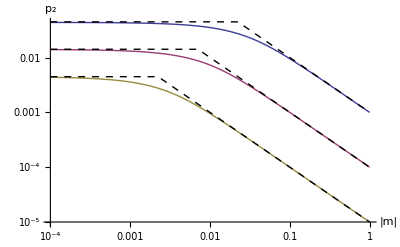

```mathematica
prescuem[m,Λ]/.Λ->{10^-3,10^-4,10^-5};
Show[LogLogPlot[%,{m,0.0001,1},PlotRange->All(*,PlotLegends->LineLegend[{"U_R = 10^-3","U_R = 10^-4","U_R = 10^-5"}]*)],LogLogPlot[If[m<√(#/2),√(2 #),#/Abs[m]]&/@{10^-3,10^-4,10^-5},{m,0.0001,1},PlotStyle->{Dashed,Black}],AxesLabel->{"|m|","p_2"}]
```

### Approximate probability of rescue: sufficiently critical single mutants

#### Approximation (equation 7 and 8)

When m<<√(Λ/2) the probability of 2-step rescue from this single mutant lineage, as calculated above, is √(2Λ). In this circumstance we can further approximate, since Λ[m] ~ Λ[0], f(m|m0) ~ f(0|m0), and pest(m)~0. So the rate of 2-step “sufficiently critical” rescue from single mutants is roughly

```mathematica
U Integrate[fm[0,m0,mmax,λ,n] √(2Λ0),{m,-√(Λ0/2),√(Λ0/2)}];
%==2U fm[0,m0,mmax,λ,n]Λ0
```

True

with Λ0 = Λ1[0,mmax,λ,n,U].

Check integration bounds:

{{m→-0.000655285},{m→0.00066309}}

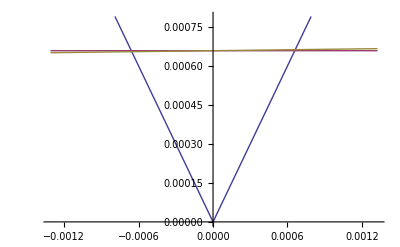

```mathematica
U=2*10^-5;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,-0.1}],mpos=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,0.1}]}
pr0=√(Λ1[0,mmax,λ,n,U]/2);

Plot[{Abs[m],pr0,√(Λ1[m,mmax,λ,n,U]/2)},{m,2m/.mneg,2m/.mpos},PlotRange->{0,1.2 pr0}]

Clear[mmax,λ,Es,n,n0,U]
```

Now check the contribution of single mutant growth rates to 2-step sufficiently critical rescue

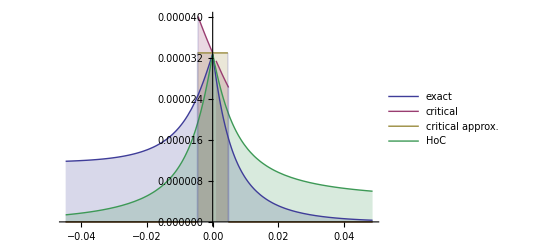

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
m0=-0.3;

{mneg=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,-0.1}],mpos=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],
fm[m,m0,mmax,λ,n](1-pest[m])√(2Λ1[m,mmax,λ,n,U])HeavisideTheta[(m-(m/.mneg))((m/.mpos)-m)],
 fm[0,m0,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U]) HeavisideTheta[(m+pr0)(pr0-m)],
fm[0,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]]
};

Plot[%,{m,10m/.mneg,10m/.mpos},PlotRange->{0,All},Filling->Bottom,PlotLegends->LineLegend[{"exact","critical","critical approx.","HoC"}]]

Clear[mmax,λ,Es,n,U,m0]
```

Finally, let’s check the total rates of rescue across all m

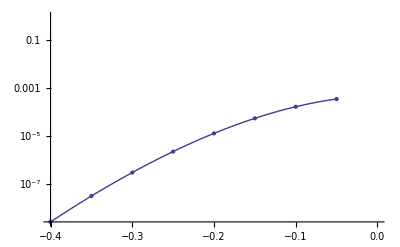

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,-0.1}],mpos=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{

Table[{m0,NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])√(2Λ1[m,mmax,λ,n,U]),{m,m/.mneg,m/.mpos}]},{m0,-0.8mmax,-0.1mmax,0.1mmax}]

};

Show[
ListLogPlot[%],
LogPlot[2 fm[0,m0,mmax,λ,n]Λ1[0,mmax,λ,n,U],{m0,-0.8mmax,-0.1mmax}]
]

Clear[mmax,λ,Es,n,U,n0]
```

#### Closed form approximation (equation 9 / equation A3)

OK, so a good approximation for sufficiently critical rescue from a mutant is

```mathematica
2 Λ0 fm[0,m0,mmax,λ,n];
```

with Λ0=Λ1[0,mmax,λ,n,U]

but note that, while this has reduced a lot of complexity, Λ0 = U ∫ f(m|0) p_est(m) dm is still an integral we have to compute. Fortunately however, we can just use the approximations Anciaux et al used (and we replicated above), so that when we take m=mmax ψ(1-ψ/4) to zero we have Λ0 as roughly

```mathematica
(*multiply by m because anciaux A12 accounts for number of individuals in lineage, which they estimate as 1/m*)
m AnciauxEqnA12/.ψwt->ψ/.m->mmax ψ(1-ψ/4)/.α->(ρmax ψ^2)/4;
Limit[%,ψ->0];
Simplify[%/.ρmax->mmax/λ,{mmax>0,λ>0}]
```

(2 U √(mmax λ))/(√π)

so that when we include mutation rate from the wildtype we have

```mathematica
4 U^2 fm[0,m0,mmax,λ,n] √(mmax λ/π);
```

We can further approximate fm to give a simpler analytic form. Using the approximation over ψ above (and incorporating the change in scale as we have integrated over fm above) we get

```mathematica
Simplify[4 U^2 √(mmax λ/π)(D[2(1-√(1-m/mmax)),m]fψ/.ψ->0)/.mmax->ρmax λ/.m->0,{λ>0,θ>1/2,ψwt<0}]/.-(ρmax ψwt^2)/4->-α(*/.θ->n/2*)/.ψwt->Subscript[ψ, 0]//Simplify
FullSimplify[U^2  (1-Subscript[ψ, 0]/2)^(1/2-θ)ⅇ^-α 2/π==%]
```

(2^(1/2+θ) ⅇ^-α U^2 (2-ψ_0)^(1/2-θ))/π

True

Check contributions across m

```mathematica
Clear[m0]
```

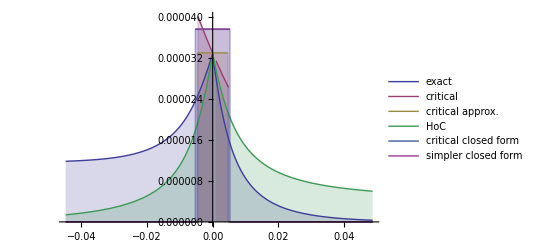

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
m0=-0.3;

{mneg=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,-0.1}],mpos=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],
fm[m,m0,mmax,λ,n](1-pest[m])√(2Λ1[m,mmax,λ,n,U])HeavisideTheta[(m-(m/.mneg))((m/.mpos)-m)],
 fm[0,m0,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U]) HeavisideTheta[(m+pr0)(pr0-m)],
fm[0,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],
fm[0,m0,mmax,λ,n] √(2 (2 U √(mmax λ))/(√π))HeavisideTheta[(m+√((U √(mmax λ))/(√π)))(√((U √(mmax λ))/(√π))-m)],
(D[2(1-√(1-m/mmax)),m]fψ/.ψ->0/.ψwt->2 (1-√(1-m0/mmax))/.ρmax->mmax/λ/.θ->n/2/.m->0)√(2 (2 U √(mmax λ))/(√π))HeavisideTheta[(m+√((U √(mmax λ))/(√π)))(√((U √(mmax λ))/(√π))-m)]
};

Plot[%,{m,10m/.mneg,10m/.mpos},PlotRange->{0,All},Filling->Bottom,PlotLegends->LineLegend[{"exact","critical","critical approx.","HoC", "critical closed form","simpler closed form"}]]

Clear[mmax,λ,Es,n,U,m0]
```

And check total rate

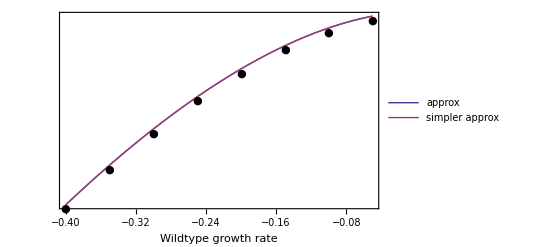

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,-0.1}],mpos=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
Table[{m0,NIntegrate[U fm[m,m0,mmax,λ,n](1-pest[m])√(2Λ1[m,mmax,λ,n,U]),{m,m/.mneg,m/.mpos}]},{m0,-0.8mmax,-0.1mmax,0.1mmax}]
};

Show[
LogPlot[
{U 2 Λ0approx fm[0,m0,mmax,λ,n],U^2  (1-Subscript[ψ, 0]/2)^(1/2-θ)ⅇ^-α 2/π/.α->ρmax Subscript[ψ, 0]^2/4/.Subscript[ψ, 0]->2 (1-√(1-m0/mmax))/.ρmax->mmax/λ/.θ->n/2},{m0,-0.8mmax,-0.1mmax},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Rate of rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"approx","simpler approx"}],Scaled@{3/4,1/4}]
],
ListLogPlot[%,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"p2CritApprox.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

### Approximate probability of rescue: sufficiently non-critical single mutants

#### Approximation 1 (equation 7)

When m>>√(Λ/2) the probability of 2-step rescue from this single mutant lineage, as calculated above, is roughly Λ/Abs[m].

We have seen above that the solutions to m^2= Λ[m]/2 can be approximated well by m=±√(Λ[0]/2).

Check the contribution of single mutant growth rates to 2-step sufficiently critical rescue

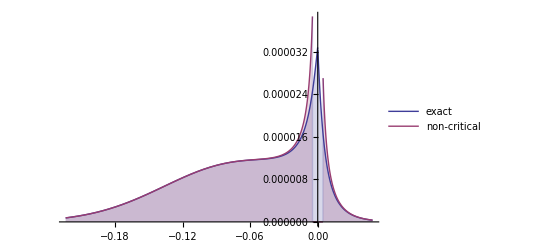

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.3;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]],
fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-pr0-m1)(pr0-m1)]

};

Plot[%,{m1,50m1/.mneg,10m1/.mpos},PlotRange->{0,All},Filling->Bottom,PlotLegends->LineLegend[{"exact","non-critical"}]]

Clear[mmax,λ,Es,n,U,mwt]
```

And let’s check the total rates of rescue across all m1

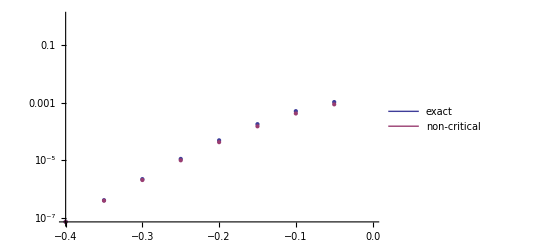

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{

Table[{mwt,NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]],{m1,mwt,mmax}]},{mwt,-0.8mmax,-0.1mmax,0.1mmax}],
Table[{mwt,NIntegrate[fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1]
,{m1,mwt,-pr0}]+NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1]
,{m1,pr0,mmax}]},{mwt,-0.8mmax,-0.1mmax,0.1mmax}]

};

Show[
ListLogPlot[%,PlotLegends->LineLegend[{"exact","non-critical"}]]
]

Clear[mmax,λ,Es,n,U,n0]
```

#### Approximation 2 (approximate Λ_1 using equation A2)

We can next borrow the approximation of Λ1 from Anciaux et al. (their eqn A12 without the 1/mwt term)

```mathematica
Abs[mwt]AnciauxEqnA12
```

(U (1-ψwt/2)^(1/2-θ) Abs[mwt] (ⅇ^-α/(√π √α)-Erfc[√α]))/(1-ψwt/4)

Check contributions of m1

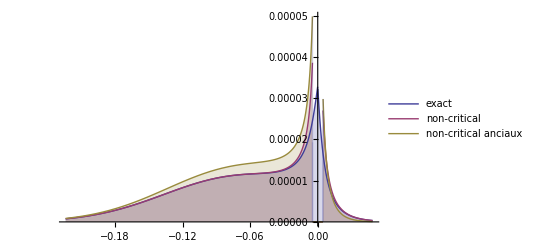

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.3;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]],
fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-pr0-m1)(pr0-m1)],
( fm[m1,mwt,mmax,λ,n](1-pest[m1])(Abs[m1] AnciauxEqnA12)/Abs[m1]/.ψwt->ψ/.m->mmax ψ(1-ψ/4)/.α->(ρmax ψ^2)/4/.ψ->2(1-√(1-m/mmax))/.ρmax->mmax/λ/.θ->n/2/.m->m1)HeavisideTheta[(-pr0-m1)(pr0-m1)]

};

Plot[%,{m1,50m1/.mneg,10m1/.mpos},PlotRange->{0,All},Filling->Bottom,PlotLegends->LineLegend[{"exact","non-critical","non-critical anciaux"}]]

Clear[mmax,λ,Es,n,U,mwt]
```

and try with smaller mwt

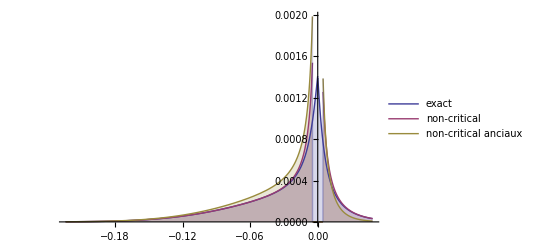

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]],
fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-pr0-m1)(pr0-m1)],
( fm[m1,mwt,mmax,λ,n](1-pest[m1])(Abs[m1] AnciauxEqnA12)/Abs[m1]/.ψwt->ψ/.m->mmax ψ(1-ψ/4)/.α->(ρmax ψ^2)/4/.ψ->2(1-√(1-m/mmax))/.ρmax->mmax/λ/.θ->n/2/.m->m1)HeavisideTheta[(-pr0-m1)(pr0-m1)]

};

Plot[%,{m1,50m1/.mneg,10m1/.mpos},PlotRange->{0,All},Filling->Bottom,PlotLegends->LineLegend[{"exact","non-critical","non-critical anciaux"}]]

Clear[mmax,λ,Es,n,U,mwt]
```

#### Closed form approximation - subcriticals (equations 10 and 11)

For the subcriticals our approximation for Λ2 is now the integral of

```mathematica
fm[m,mwt,mmax,λ,n]AnciauxEqnA12
```

-(ⅇ^((m-2 mmax+mwt)/λ) U ((-m+mmax)/λ)^(n/2) (1-ψwt/2)^(1/2-θ) (ⅇ^-α/(√π √α)-Erfc[√α]) Hypergeometric0F1Regularized[n/2,((-m+mmax) (mmax-mwt))/λ^2])/((m-mmax) (1-ψwt/4))

over m from -∞ to -m*, with α dependent on m.

As before we can approximately write fm in the ψ scale, leaving us with the integral of

```mathematica
fψ AnciauxEqnA12/.α->(ρmax ψ^2)/4
constant=(U √ρmax)/(2 √π (1-ψwt/4)(1-ψwt/2)^(-1+2θ));
ψterm=ⅇ^(-1/4 ρmax (ψ-ψwt)^2)  (1-ψ/2)^(-1/2+θ) ((2 ⅇ^(-(ρmax ψ^2)/4))/(√π √(ρmax ψ^2))-Erfc[(√(ρmax ψ^2))/2]);
Simplify[(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) U √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ) (1-ψwt/2)^(1/2-θ) ((2 ⅇ^(-(ρmax ψ^2)/4))/(√π √(ρmax ψ^2))-Erfc[(√(ρmax ψ^2))/2]))/(2 √π (1-ψwt/4))==constant ψterm,{ψwt<0}]
```

(ⅇ^(-1/4 ρmax (ψ-ψwt)^2) U √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ) (1-ψwt/2)^(1/2-θ) ((2 ⅇ^(-(ρmax ψ^2)/4))/(√π √(ρmax ψ^2))-Erfc[(√(ρmax ψ^2))/2]))/(2 √π (1-ψwt/4))

True

over ψ between -∞ and ψ*

```mathematica
Simplify[2(1-√(1-m/mmax))/.m->{-∞,-SuperStar[m]},mmax>0]
```

{-∞,2-2 √((0.00466097+mmax)/mmax)}

We make 2 different approximations. When ψ-ψwt and ψ ρmax = ψ mmax/λ=ψ(mmax*n)/(2Es) are really small we have

```mathematica
ψterm/.ψ-ψwt->ψwt+dψ ϵ /.ψ->ψ ϵ;
Simplify[Normal[Series[%,{ϵ,0,-1}]]/.ϵ->1,{ψ<0}]
```

-(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ)

And when ψ is small but ρmax is really large we have

```mathematica
ψterm/.ρmax->ρmax /ϵ;
Simplify[Normal[Series[%,{ϵ,0,2}]]/.ϵ->1,{ψ<0}]/.(1-ψ/2)^θ->1/. 2 π-π ψ-> 2 π
```

-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3)

Compare numerically over m (from ψwt to ψ*)

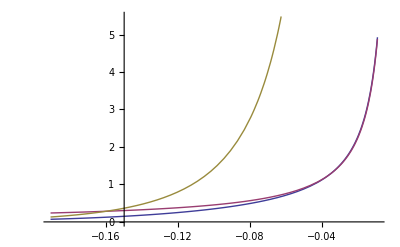

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.1;
SuperStar[m]=√(Λ1[0,mmax,λ,n,U]/2);

{ψterm, -(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ),-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3)}/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax));
Plot[%,{ψ,2(1-√(1-mwt/mmax)),2-2 √((mmax+SuperStar[m])/mmax)},PlotRange->{0,Automatic}]

Clear[mmax,λ,Es,n,U,mwt]
```

And compare integrals across range of mwt. We see the nice transition from the small ψ approx to the large ρmax approx as we increase ρmax:

For ρmax = 10

10.

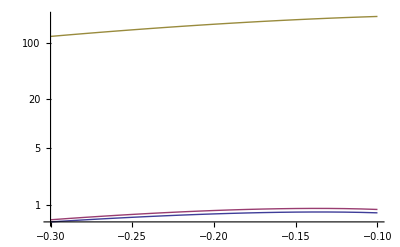

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.1;
n=4;
SuperStar[m]=√(Λ1[0,mmax,λ,n,U]/2);
mmax/λ

{ψterm, -(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ),-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3)}/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax));
Table[Table[{mwt,NIntegrate[%[[i]],{ψ,2(1-√(1-mwt/mmax)),2-2 √((mmax+SuperStar[m])/mmax)}]},{mwt,-0.3,-0.1,0.01}],{i,Length[%]}];
ListLogPlot[%,Joined->True]

Clear[mmax,λ,Es,n,U,mwt]
```

For ρmax=100

100.

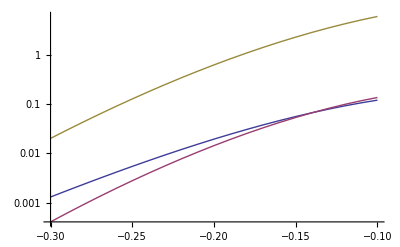

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
SuperStar[m]=√(Λ1[0,mmax,λ,n,U]/2);
mmax/λ

{ψterm, -(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ),-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3)}/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax));
Table[Table[{mwt,NIntegrate[%[[i]],{ψ,2(1-√(1-mwt/mmax)),2-2 √((mmax+SuperStar[m])/mmax)}]},{mwt,-0.3,-0.1,0.01}],{i,Length[%]}];
ListLogPlot[%,Joined->True]

Clear[mmax,λ,Es,n,U,mwt]
```

for ρmax=1000

1000.

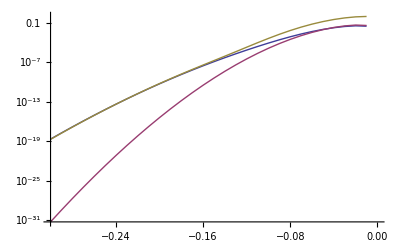

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.001;
n=4;
SuperStar[m]=√(Λ1[0,mmax,λ,n,U]/2);
mmax/λ

{ψterm, -(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ),-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3)}/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax));
Table[Table[{mwt,NIntegrate[%[[i]],{ψ,2(1-√(1-mwt/mmax)),2-2 √((mmax+SuperStar[m])/mmax)}]},{mwt,-0.3,-0.01,0.01}],{i,Length[%]}];
ListLogPlot[%,Joined->True,PlotRange->All]

Clear[mmax,λ,Es,n,U,mwt]
```

and for ρmax=10000

10000.

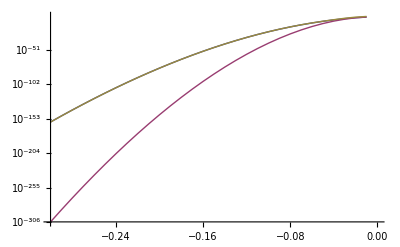

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.0001;
n=4;
SuperStar[m]=√(Λ1[0,mmax,λ,n,U]/2);
mmax/λ

{ψterm, -(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ),-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3)}/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax));
Table[Table[{mwt,NIntegrate[%[[i]],{ψ,2(1-√(1-mwt/mmax)),2-2 √((mmax+SuperStar[m])/mmax)}]},{mwt,-0.3,-0.01,0.01}],{i,Length[%]}];
ListLogPlot[%,Joined->True,PlotRange->All]

Clear[mmax,λ,Es,n,U,mwt]
```

Right, so for the small ψ approx we need to integrate

```mathematica
smallψapprox=-(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ);
```

which has a simple expression if we do not integrate all the way back to -∞

```mathematica
Integrate[smallψapprox,{ψ,a,b},Assumptions->{a<b<0}]
```

-(2 ⅇ^(-(ρmax ψwt^2)/4) Log[b/a])/(√π √ρmax)

And for the large ρmax we need to integrate

```mathematica
largeρapprox=-(4 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψ^3);
```

here we can again use the Laplace approx with

```mathematica
q[ψ_]:=-1/4 ρmax (ψ^2+(ψ-ψwt)^2)
h[ψ_]:=-4/(√π ρmax^(3/2) ψ^3)
```

and we know that q is peaked at

```mathematica
Solve[D[q[ψ],ψ]==0,ψ]
```

{{ψ→ψwt/2}}

where h equals

```mathematica
h[ψwt/2]
```

-32/(√π ρmax^(3/2) ψwt^3)

giving

```mathematica
h[ψwt/2]Exp[q[ψ]]
verylargeρapprox=-(32 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψwt^3);
```

-(32 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψwt^3)

Numerical check

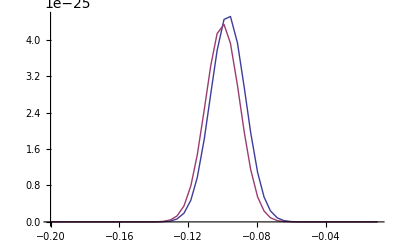

```mathematica
{largeρapprox,verylargeρapprox}/.ρmax->10000/.ψwt->-0.2;
Plot[%,{ψ,-0.2,-0.01},PlotRange->All]
```

which we can integrate over all ψ with little error (because exponential tails)

```mathematica
Integrate[verylargeρapprox,{ψ,-∞,∞},Assumptions->{ρmax>0,ψwt<0}]
```

-(32 √2 ⅇ^(-(ρmax ψwt^2)/8))/(ρmax^2 ψwt^3)

OK, so our small ρmax approx for the probability of 2-step subcritical rescue is

```mathematica
smallψapproxRescueψ=constant Integrate[smallψapprox,{ψ,a,b},Assumptions->{a<b<0}]
smallψapproxRescue=%/.a->2(1-√(1-mwt/mmax))/.b-> 2(1- √(1+mstar/mmax))/.mstar->√(Λ0approx/2)/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))
```

-(ⅇ^(-(ρmax ψwt^2)/4) U (1-ψwt/2)^(1-2 θ) Log[b/a])/(π (1-ψwt/4))

-(ⅇ^(-(mmax (1-√(1-mwt/mmax))^2)/λ) (1-mwt/mmax)^((1-n)/2) U Log[(1-√(1+(√(U √(mmax λ)))/(mmax π^(1/4))))/(1-√(1-mwt/mmax))])/((1+1/2 (-1+√(1-mwt/mmax))) π)

and our very large ρmax approx for the probability of 2-step subcritical rescue is

```mathematica
verylargeρapproxRescueψ=constant Integrate[verylargeρapprox,{ψ,-∞,∞},Assumptions->{ρmax>0,ψwt<0}]
verylargeρapproxRescue=%/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))
```

-(16 ⅇ^(-(ρmax ψwt^2)/8) √(2/π) U (1-ψwt/2)^(1-2 θ))/(ρmax^(3/2) (1-ψwt/4) ψwt^3)

-(2 ⅇ^(-(mmax (1-√(1-mwt/mmax))^2)/(2 λ)) (1-mwt/mmax)^((1-n)/2) √(2/π) U)/((1-√(1-mwt/mmax))^3 (1+1/2 (-1+√(1-mwt/mmax))) (mmax/λ)^(3/2))

Check formula for text

```mathematica
Simplify[smallψapproxRescueψ==U(1-ψwt/2)^(1-2 θ)/(1-ψwt/4)ⅇ^-α Log[a/b]/π/.α->ρmax ψwt^2/4,{a<b<0}]
Simplify[verylargeρapproxRescueψ==(-U(1-ψwt/2)^(1-2 θ)/(1-ψwt/4)(ⅇ^-α 1/((α/2 )^3 π))^(1/2)/.α->ρmax ψwt^2/4),{ρmax>0,ψwt>0}]
```

True

True

Compare to better approximation

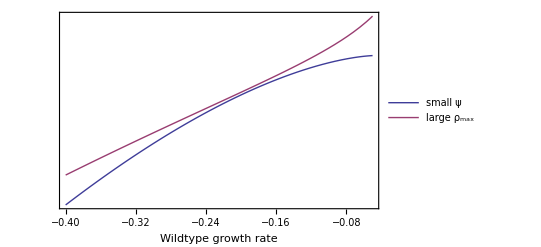

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
Table[{mwt,U NIntegrate[fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1]
,{m1,mwt,-pr0}]},{mwt,-0.8mmax,-0.1mmax,0.1mmax}]
};


Show[
LogPlot[
{U smallψapproxRescue,U verylargeρapproxRescue},{mwt,-0.8mmax,-0.1mmax},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Rate of rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"small ψ","large ρ_max"}],Scaled@{3/4,1/4}]
](*,
ListLogPlot[%,PlotMarkers->{Automatic,Medium},PlotStyle->Black]*)
]

(*Export[imagedir<>"p2SubApprox.pdf",%];*)

Clear[mmax,λ,Es,n,U,n0]
```

#### Closed form approximation - supercriticals (equation 12)

For the supercriticals our approximation for Λ2 is now the integral of

```mathematica
fm[m,mwt,mmax,λ,n](1-pest[m])AnciauxEqnA12
```

-(ⅇ^(-2 m+(m-2 mmax+mwt)/λ) U ((-m+mmax)/λ)^(n/2) (1-ψwt/2)^(1/2-θ) (ⅇ^-α/(√π √α)-Erfc[√α]) Hypergeometric0F1Regularized[n/2,((-m+mmax) (mmax-mwt))/λ^2])/((m-mmax) (1-ψwt/4))

over m from m^* to m_max, with α dependent on m.

As before we can approximately write fm in the ψ scale, leaving us with the integral of

```mathematica
fψ(1-pest[m]) AnciauxEqnA12/.α->(ρmax ψ^2)/4/.m-> mmax (1-ψ/4) ψ
constant=(U √ρmax)/(2 √π (1-ψwt/4)(1-ψwt/2)^(-1+2θ));
ψterm=ⅇ^(-2 mmax (1-ψ/4) ψ-1/4 ρmax (ψ-ψwt)^2)  (1-ψ/2)^(-1/2+θ) ((2 ⅇ^(-(ρmax ψ^2)/4))/(√π √(ρmax ψ^2))-Erfc[(√(ρmax ψ^2))/2]);
Simplify[(fψ(1-pest[m]) AnciauxEqnA12/.α->(ρmax ψ^2)/4/.m-> mmax (1-ψ/4) ψ)==constant ψterm ,{ψwt<0}]
```

(ⅇ^(-2 mmax (1-ψ/4) ψ-1/4 ρmax (ψ-ψwt)^2) U √ρmax ((2-ψ)/(2-ψwt))^(-1/2+θ) (1-ψwt/2)^(1/2-θ) ((2 ⅇ^(-(ρmax ψ^2)/4))/(√π √(ρmax ψ^2))-Erfc[(√(ρmax ψ^2))/2]))/(2 √π (1-ψwt/4))

True

over ψ between ψ* and 2

```mathematica
Clear[m]
Simplify[2(1-√(1-m/mmax))/.m->{mstar,mmax},mmax>0]
```

{2-2 √(1-mstar/mmax),2}

Here we only need one approximation as large m single mutants will establish themselves and are unlikely to rescue. So we just look at when ψ-ψwt and ψ ρmax = ψ mmax/λ=ψ(mmax*n)/(2Es) are really small, giving

```mathematica
ψterm /.ψ->ψ ϵ;
Simplify[Normal[Series[%,{ϵ,0,-1}]]/.ϵ->1,{ψ>0}]
```

(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ)

Right, so for the small ψ approx we need to integrate

```mathematica
smallψapprox=(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ);
```

which has a simple expression

```mathematica
Integrate[smallψapprox,{ψ,a,b},Assumptions->{0<a<b<2}]
```

(2 ⅇ^(-(ρmax ψwt^2)/4) Log[b/a])/(√π √ρmax)

OK, so our small ρmax approx for the probability of 2-step supercritical rescue is

```mathematica
smallψapproxRescueSuperψ=constant Integrate[smallψapprox,{ψ,a,b},Assumptions->{0<a<b}]
smallψapproxRescueSuper=%/.a->2( 1- √(1-mstar/mmax))/.b->(√2)/(√ρmax)/.mstar->√(Λ0approx/2)/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))
```

(ⅇ^(-(ρmax ψwt^2)/4) U (1-ψwt/2)^(1-2 θ) Log[b/a])/(π (1-ψwt/4))

(ⅇ^(-(mmax (1-√(1-mwt/mmax))^2)/λ) (1-mwt/mmax)^((1-n)/2) U Log[1/(√2 √(mmax/λ) (1-√(1-(√(U √(mmax λ)))/(mmax π^(1/4)))))])/((1+1/2 (-1+√(1-mwt/mmax))) π)

where we’ve used our rough cut-off  of √(2/ρmax), after which the rate of rescue declines very very quickly and therefore is negligible.

Check formula in text

```mathematica
Simplify[(U (1-ψwt/2)^(1-2 θ))/(1-ψwt/4)ⅇ^-α Log[b/a]/π==smallψapproxRescueSuperψ/.α->(ρmax ψwt^2)/4]
```

True

Compare to better approximation

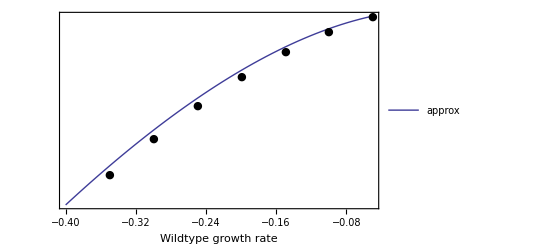

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
Table[{mwt,U NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1]
,{m1,pr0,mmax}]},{mwt,-0.8mmax,-0.1mmax,0.1mmax}]
};

Show[
LogPlot[
{U smallψapproxRescueSuper},{mwt,-0.8mmax,-0.1mmax},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Rate of rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"approx"}],Scaled@{3/4,1/4}]
],
ListLogPlot[%,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"p2SuperApprox.pdf",%];*)

Clear[mmax,λ,Es,n,U,n0]
```

### Plot approximations (figure 5)

We can now quickly compare the (approximate) rates through each type of 2-step rescue

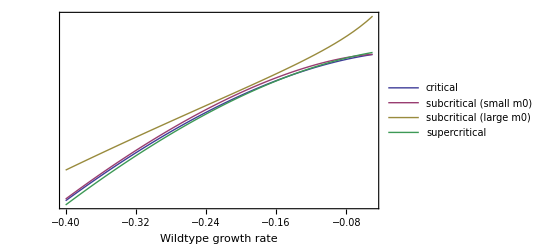

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

Show[
LogPlot[
{ 2 Λ0approx fm[0,mwt,mmax,λ,n],smallψapproxRescue,verylargeρapproxRescue,smallψapproxRescueSuper},{mwt,-0.8mmax,-0.1mmax},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Rate of rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"critical","subcritical (small m0)","subcritical (large m0)","supercritical"}],Scaled@{3/4,1/4}]
]
]

(*Export[imagedir<>"p2SuperApprox.pdf",%];*)

Clear[mmax,λ,Es,n,U,n0]
```

or in terms of relative contributions

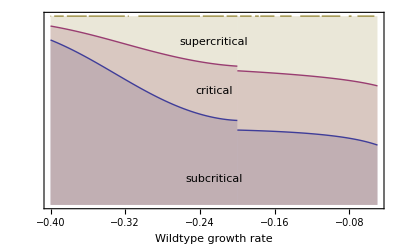

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{verylargeρapproxRescue, 2 Λ0approx fm[0,mwt,mmax,λ,n],smallψapproxRescueSuper};
%/Total[%];
Accumulate[%];
largem0plot=
Plot[
%,{mwt,-0.8mmax,-0.2},
PlotRange->{0,1},
PlotStyle->Thick,
Filling->Bottom,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Relative contribution"},
FrameTicks->{True,False,False,All},
LabelStyle->labelstyle
];

(*Export[imagedir<>"p2SuperApprox.pdf",%];*)

{smallψapproxRescue, 2 Λ0approx fm[0,mwt,mmax,λ,n],smallψapproxRescueSuper};
%/Total[%];
Accumulate[%];
smallm0plot=
Plot[
%,{mwt,-0.2,-0.1mmax},
PlotRange->{0,1},
PlotStyle->Thick,
Filling->Bottom,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Relative contribution"},
FrameTicks->{True,False,False,All},
LabelStyle->labelstyle
];

Show[largem0plot,smallm0plot,PlotRange->All,
Epilog->{
Text["subcritical",Scaled@{0.5,0.15}],
Text["critical",Scaled@{0.5,0.6}],
Text["supercritical",Scaled@{0.5,0.85}]
}
]

Clear[mmax,λ,Es,n,U,n0]
```

Compare with better approximations

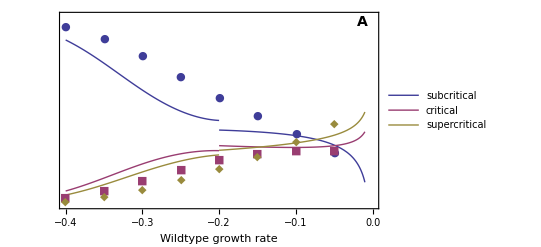

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

xs=Table[mwt,{mwt,-0.8mmax,-0.1mmax,0.1mmax}];

temptab={
Table[ NIntegrate[fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1]
,{m1,mwt,-pr0}],{mwt,-0.8mmax,-0.1mmax,0.1mmax}],
Table[NIntegrate[ fm[m1,mwt,mmax,λ,n](1-pest[m1])√(2Λ1[m1,mmax,λ,n,U]),{m1,m1/.mneg,m1/.mpos}],{mwt,-0.8mmax,-0.1mmax,0.1mmax}],
Table[NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1]
,{m1,pr0,mmax}],{mwt,-0.8mmax,-0.1mmax,0.1mmax}]
};
Transpose[temptab];
Table[%[[i]]/Total[%[[i]]],{i,Length[%]}];
test=Transpose[%];
(*Accumulate[%]*)
data=Table[Transpose[Join[{xs},{%[[i]]},1]],{i,Length[%]}];

{smallψapproxRescue,2 Λ0approx fm[0,mwt,mmax,λ,n] ,smallψapproxRescueSuper};
%/Total[%];

{verylargeρapproxRescue,2 Λ0approx fm[0,mwt,mmax,λ,n] ,smallψapproxRescueSuper};
%/Total[%];
Show[
Plot[
%,{mwt,-0.4,-0.2},
PlotRange->{0,1},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Percent of 2-step rescues"},
FrameTicks->{True,False,False,All},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"subcritical","critical","supercritical"}],Scaled@{3/4,3/4}],
Epilog->Text[Style["A",14,Bold],Scaled@{0.95,0.95}]
],
Plot[
%%%,{mwt,-0.2,-0.01},
PlotRange->{0,1},
PlotStyle->Thick
],
ListPlot[data,PlotMarkers->{Automatic,Medium},PlotRange->{0,1}],
PlotRange->{{-0.4,0},{0,1}}
]

(*Export[imagedir<>"p2RelContrGrowth.pdf",%];*)

Clear[mmax,λ,Es,n,U,n0]
```

or across mutation rate for a given m0

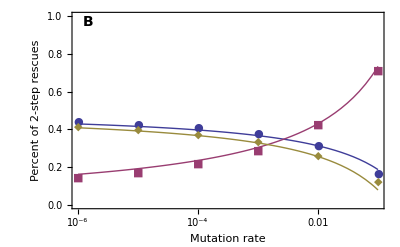

```mathematica
n0=10^4;
mwt=-0.1;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
U=10^x;

xs=Table[U,{x,-6,-1,1}];

temptab2=Table[
mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}];
mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}];
pr0=√(Λ1[0,mmax,λ,n,U]/2);
{ 
NIntegrate[fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1],{m1,mwt,-pr0}],
NIntegrate[ fm[m1,mwt,mmax,λ,n](1-pest[m1])√(2Λ1[m1,mmax,λ,n,U]),{m1,m1/.mneg,m1/.mpos}],
NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1],{m1,pr0,mmax}]
}
,{x,-6,-1,1}];

temptab2;
Table[%[[i]]/Total[%[[i]]],{i,Length[%]}];
test=Transpose[%];
(*Accumulate[%]*)
data=Table[Transpose[Join[{xs},{%[[i]]},1]],{i,Length[%]}];

Clear[U]
{smallψapproxRescue(*verylargeρapproxRescue*),2 Λ0approx fm[0,mwt,mmax,λ,n] ,smallψapproxRescueSuper};
%/Total[%];
(*Accumulate[%];*)
Show[
LogLinearPlot[
%,{U,10^-6,10^-1},
PlotRange->{0,1},
PlotStyle->Thick,
Frame->{True,True,False,False},
FrameLabel->{"Mutation rate","Percent of 2-step rescues",,},
FrameTicks->{True,True,False,False},
LabelStyle->labelstyle,
Epilog->Text[Style["B",14,Bold],Scaled@{0.05,0.95}]
],
ListLogLinearPlot[data,PlotMarkers->{Automatic,Medium},PlotRange->{0,1}]
]

(*Export[imagedir<>"p2RelContrMutationSlow.pdf",%];*)

Clear[mmax,λ,Es,n,mwt,n0,U]
```

and with a more negative m0

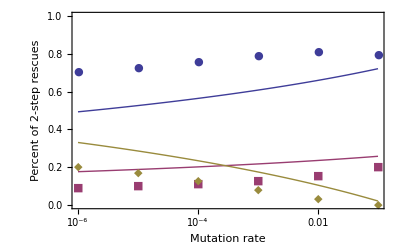

```mathematica
n0=10^4;
mwt=-0.3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
U=10^x;

xs=Table[U,{x,-6,-1,1}];

temptab3=Table[
mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}];
mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}];
pr0=√(Λ1[0,mmax,λ,n,U]/2);
{ 
NIntegrate[fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1],{m1,mwt,-pr0}],
NIntegrate[ fm[m1,mwt,mmax,λ,n](1-pest[m1])√(2Λ1[m1,mmax,λ,n,U]),{m1,m1/.mneg,m1/.mpos}],
NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1],{m1,pr0,mmax}]
}
,{x,-6,-1,1}];
temptab3;
Table[%[[i]]/Total[%[[i]]],{i,Length[%]}];
test=Transpose[%];
(*Accumulate[%]*)
data=Table[Transpose[Join[{xs},{%[[i]]},1]],{i,Length[%]}];

Clear[U]
{verylargeρapproxRescue,2 Λ0approx fm[0,mwt,mmax,λ,n] ,smallψapproxRescueSuper};
%/Total[%];
(*Accumulate[%];*)
Show[
LogLinearPlot[
%,{U,10^-6,10^-1},
PlotRange->{0,1},
PlotStyle->Thick,
Frame->{True,True,False,False},
FrameLabel->{"Mutation rate","Percent of 2-step rescues",,},
FrameTicks->{True,True,False,False},
LabelStyle->labelstyle
],
ListLogLinearPlot[data,PlotMarkers->{Automatic,Medium},PlotRange->{0,1}]
]

(*Export[imagedir<>"p2RelContrMutationFast.pdf",%];*)

Clear[mmax,λ,Es,n,mwt,n0,U]
```

and sum them to get the total rate of rescue

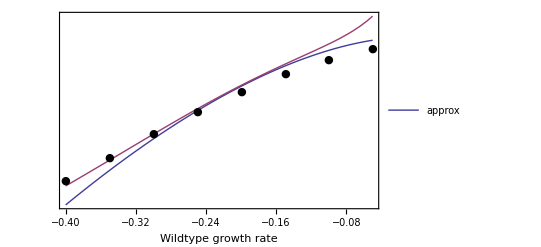

```mathematica
n0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

{
Table[{mwt, NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]]
,{m1,-∞,mmax}]},{mwt,-0.8mmax,-0.1mmax,0.1mmax}]
};

{
Total[{ 2 Λ0approx fm[0,mwt,mmax,λ,n],smallψapproxRescue,smallψapproxRescueSuper}],
Total[{ 2 Λ0approx fm[0,mwt,mmax,λ,n],verylargeρapproxRescue,smallψapproxRescueSuper}]
};

Show[
LogPlot[
%,{mwt,-0.8mmax,-0.1mmax},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Rate of rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"approx"}],Scaled@{3/4,1/4}]
],
ListLogPlot[%%,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"p2SuperApprox.pdf",%];*)

Clear[mmax,λ,Es,n,U,n0]
```

or use this rate to get the total probability of rescue

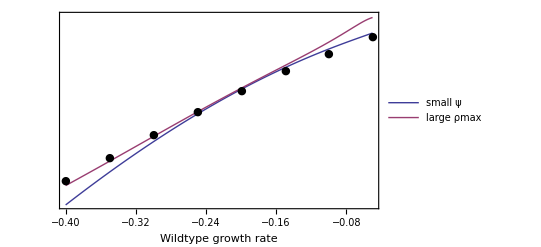

```mathematica
N0=10^4;
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);

tab={
Table[{
mwt, 
prescue/.p0->prescuem[mwt,U NIntegrate[fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]],{m1,-∞,mmax}]]
},{mwt,-0.8mmax,-0.1mmax,0.1mmax}]
};

{
prescue/.p0->prescuem[mwt,U Total[{ 2 Λ0approx fm[0,mwt,mmax,λ,n],smallψapproxRescue,smallψapproxRescueSuper}]],
prescue/.p0->prescuem[mwt,U Total[{ 2 Λ0approx fm[0,mwt,mmax,λ,n],verylargeρapproxRescue,smallψapproxRescueSuper}]]
};
Show[
LogPlot[
{%,},{mwt,-0.8mmax,-0.1mmax},
PlotStyle->Thick,
Frame->{True,False,False,True},
FrameLabel->{"Wildtype growth rate",,,"Probability of 2-step rescue"},
FrameTicks->{True,False,False,True},
LabelStyle->labelstyle,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"small ψ","large ρmax"}],Scaled@{3/4,1/4}]
],
ListLogPlot[tab,PlotMarkers->{Automatic,Medium},PlotStyle->Black]
]

(*Export[imagedir<>"p2TotalApprox.pdf",%];
*)
Clear[mmax,λ,Es,n,U,N0]
```

## Distribution of growth rates given rescue

### Distribution of growth rates among 1-step rescue mutants (equations 13 and 14)

The distribution of growth rates among the rescue mutants in 1-step rescue is simply

```mathematica
g1m=(U fm[m,mwt,mmax,λ,n]pest[m])/Λ1[mwt,mmax,λ,n,U];
```

We can approximate this using our Laplacian approach. In this case we have

```mathematica
h[ψ_]:=  ((1-ψ/2)/(1-ψwt/2))^(θ-1/2)(1-ⅇ^(-2 mmax y))/.y->ψ(1-ψ/4)
q[ψ_]:=1/4 (ψ-ψwt)^2
h0=Normal[Series[h[ψ],{ψ,0,1}]];
g1mapprox=Simplify[(U/-mwt(√ρmax)/(2 √π)h0 Exp[-ρmax q[ψ]])/AnciauxEqnA12/.mwt->mmax(4-ψwt)ψwt/4,{ψwt<0,α>0,ρmax>0}]
```

(ⅇ^(α-1/4 ρmax (ψ-ψwt)^2) √(α ρmax) ψ)/(ψwt (-1+ⅇ^α √π √α Erfc[√α]))

And if we want to plot on an m scale (and still want a pdf) we need to scale by

```mathematica
scaleg1approx=D[2(1-√(1-m/mmax)),m]
```

1/(√(1-m/mmax) mmax)

giving

```mathematica
g1mApp=scaleg1approx g1mapprox;
```

Numerically compare

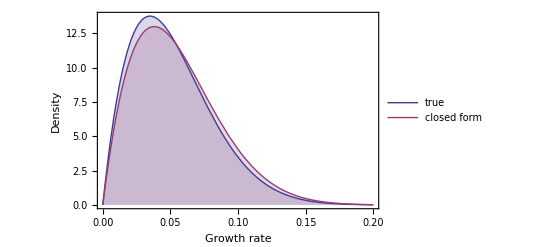

```mathematica
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.1;
{
g1m,
g1mApp
}/.α->ψwt^2 ρmax/4/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax));

Plot[%,{m,-0.2,0.2},PlotRange->{0,All},Frame->{True,True,False,False},FrameLabel->{"Growth rate","Density"},PlotLegends->Placed[{"true","closed form"},Top],Filling->Bottom,LabelStyle->labelstyle]

Clear[mmax,λ,Es,n,mwt]
```

### Distribution of growth rates among 2-step rescue genotypes (equation 15)

The rate of 2-step rescue through double mutants with growth rate m2 is

```mathematica
g2numerator[m0_,m2_?NumericQ]:=U NIntegrate[fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,U fm[m2,m,mmax,λ,n]pest[m2]],{m,-∞,mmax}];
```

Integrating this over m2 then provides the correct normalization,

```mathematica
g2denominator[m0_?NumericQ]:=NIntegrate[U fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,U fm[m2,m,mmax,λ,n]pest[m2]],{m,-∞,mmax},{m2,0,mmax}];
```

### Plot growth rates of rescue genotypes (figure 6)

```mathematica
xmin=-0.3;
xmax=0.25;
ymax=28;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

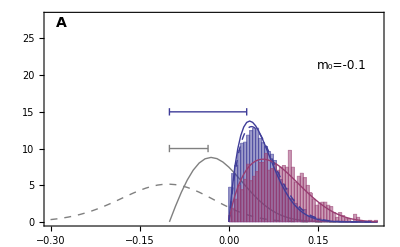

```mathematica
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.1;

{
(*random*)
Table[{m2,fm[m2,mwt,mmax,λ,n]},{m2,xmin,xmax,0.01}],
(*established*)
Table[{m2,(fm[m2,mwt,mmax,λ,n]pest[m2-mwt])/NIntegrate[fm[m2,mwt,mmax,λ,n]pest[m2-mwt],{m2,mwt,mmax}]},{m2,mwt,xmax,0.01}]
};
oldtheory=ListPlot[%,PlotRange->All,Joined->True,PlotStyle->{Directive[Thick,Gray,Dashed],Directive[Thick,Gray]},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"random","established"}],Scaled@{1.5/8,1/2}]];

{
(*1 step*)
Table[{m2,g1m/.m->m2},{m2,0,xmax,0.005}],
(*2 step*)
total=Re[g2denominator[mwt]];
Table[{m2,1/total g2numerator[mwt,m2]},{m2,0,xmax,0.005}]
};
theory=ListPlot[%,PlotRange->All,Joined->True,PlotStyle->Thick,PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"1-step","2-step"}],Scaled@{1.5/8,1/2}]];

g1mApp/.α->ψwt^2 ρmax/4/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax));
onestepapp=Plot[%,{m,0,xmax},PlotStyle->{Thick,Dashed},PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"1-step approx."}],Scaled@{1.5/8,1/2}]];

dat=Import[datadir<>"dfe_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mwt-0.10_mutmax10_nreps10000.csv"];
onestep=Select[dat,#[[2]]==1&][[All,1]];
twostep=Select[dat,#[[2]]==2&][[All,1]];
data=Histogram[{onestep,twostep},50,"PDF",AxesOrigin->{0,0}];

Show[oldtheory,data,theory,onestepapp,
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,False,False,False},
LabelStyle->labelstyle,
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style["m_0="<>ToString[mwt],12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
{Directive[Gray,Thick],Line[{{mwt,10},{-0.035,10}}]},
{Directive[Gray,Thick],Line[{{mwt,9.5},{mwt,10.5}}]},
{Directive[Gray,Thick],Line[{{-0.035,9.5},{-0.035,10.5}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{mwt,15},{0.03,15}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{mwt,14.5},{mwt,15.5}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{0.03,14.5},{0.03,15.5}}]}
}
]

(*Export[imagedir<>"2step_m2_smallm0_sims.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

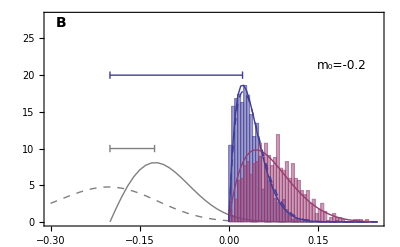

```mathematica
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

{
(*random*)
Table[{m2,fm[m2,mwt,mmax,λ,n]},{m2,xmin,xmax,0.01}],
(*established*)
Table[{m2,(fm[m2,mwt,mmax,λ,n]pest[m2-mwt])/NIntegrate[fm[m2,mwt,mmax,λ,n]pest[m2-mwt],{m2,mwt,mmax}]},{m2,mwt,xmax,0.01}]
};
oldtheory=ListPlot[%,PlotRange->All,Joined->True,PlotStyle->{Directive[Thick,Gray,Dashed],Directive[Thick,Gray]},PerformanceGoal->"Speed"];

{
(*1 step*)
Table[{m2,g1m/.m->m2},{m2,0,xmax,0.005}],
(*2 step*)
total=Re[g2denominator[mwt]];
Table[{m2,1/total g2numerator[mwt,m2]},{m2,0,xmax,0.005}]
};
theory=ListPlot[%,PlotRange->All,Joined->True,PlotStyle->Thick,PerformanceGoal->"Speed"];

g1mApp/.α->ψwt^2 ρmax/4/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax));
onestepapp=Plot[%,{m,0,xmax},PlotStyle->{Thick,Dashed}];

dat=Import[datadir<>"dfe_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mwt-0.20_mutmax10_nreps100000.csv"];
onestep=Select[dat,#[[2]]==1&][[All,1]];
twostep=Select[dat,#[[2]]==2&][[All,1]];
data=Histogram[{onestep,twostep},50,"PDF",AxesOrigin->{0,0}];

Show[oldtheory,data,theory,onestepapp,
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,False,False,False},
LabelStyle->labelstyle,
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style["m_0="<>ToString[mwt],12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],
Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
{Directive[Gray,Thick],Line[{{mwt,10},{-0.125,10}}]},
{Directive[Gray,Thick],Line[{{mwt,9.5},{mwt,10.5}}]},
{Directive[Gray,Thick],Line[{{-0.125,9.5},{-0.125,10.5}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{mwt,20},{0.023,20}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{mwt,20-0.5},{mwt,20+0.5}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{0.023,20-0.5},{0.023,20+0.5}}]}
}
]

(*Export[imagedir<>"2step_m2_medm0_sims.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

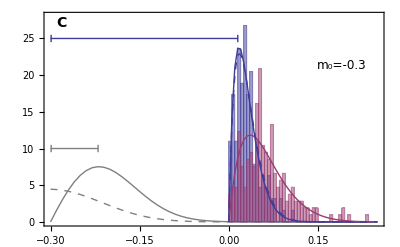

```mathematica
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.3;

{
(*random*)
Table[{m2,fm[m2,mwt,mmax,λ,n]},{m2,xmin,xmax,0.01}],
(*established*)
Table[{m2,(fm[m2,mwt,mmax,λ,n]pest[m2-mwt])/NIntegrate[fm[m2,mwt,mmax,λ,n]pest[m2-mwt],{m2,mwt,mmax}]},{m2,mwt,xmax,0.01}]
};
oldtheory=ListPlot[%,PlotRange->All,Joined->True,PlotStyle->{Directive[Thick,Gray,Dashed],Directive[Thick,Gray]},PerformanceGoal->"Speed"];

{
(*1 step*)
Table[{m2,g1m/.m->m2},{m2,0,xmax,0.005}],
(*2 step*)
total=Re[g2denominator[mwt]];
Table[{m2,1/total g2numerator[mwt,m2]},{m2,0,xmax,0.005}]
};
theory=ListPlot[%,PlotRange->All,Joined->True,PlotStyle->Thick,PerformanceGoal->"Speed"];

g1mApp/.α->ψwt^2 ρmax/4/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax));
onestepapp=Plot[%,{m,0,xmax},PlotStyle->{Thick,Dashed}];

dat=Import[datadir<>"dfe_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mwt-0.30_mutmax10_nreps1000000.csv"];
onestep=Select[dat,#[[2]]==1&][[All,1]];
twostep=Select[dat,#[[2]]==2&][[All,1]];
data=Histogram[{onestep,twostep},50,"PDF",AxesOrigin->{0,0}];

Show[oldtheory,data,theory,onestepapp,
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,False,False,False},
FrameLabel->{"Growth rate"},
LabelStyle->labelstyle,Epilog->{
Text[Style["m_0="<>ToString[mwt],12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],
Text[Style["C",14,Bold],Scaled@{0.05,0.95}],
{Directive[Gray,Thick],Line[{{mwt,10},{-0.22,10}}]},
{Directive[Gray,Thick],Line[{{mwt+0.001,9.5},{mwt+0.001,10.5}}]},
{Directive[Gray,Thick],Line[{{-0.22,9.5},{-0.22,10.5}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{mwt,25},{0.015,25}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{mwt+0.001,25-0.5},{mwt+0.001,25+0.5}}]},
{Directive[defaultcolors[[1]],Thick],Line[{{0.015,25-0.5},{0.015,25+0.5}}]}
}
]

(*Export[imagedir<>"2step_m2_largem0_sims.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

```mathematica
Clear[ymax,xmin,xmax]
```

### Distribution of first-step growth rates in 2-step rescue genotypes (equation 16)

As, in the 1-step case, we can use the Λ2 term to write the distribution of growth rates of rescue genotypes

```mathematica
h2[m_?NumericQ,m0_]:=(U fm[m,m0,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]])/Λ2[m0,mmax,λ,n,U]
```

We can also use our approximations above to get a closed form approximation for this.

For sufficiently subcritical m near -m* we have

```mathematica
smallψapprox=-(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ);
Integrate[smallψapprox,{ψ,a,b},Assumptions->{a<b<0}];
smallψapprox/%
D[2(1-√(1-m/mmax)),m]%/.a->2(1-√(1-mwt/mmax))/.b-> 2(1- √(1+mstar/mmax))/.mstar->√(Λ0approx/2)/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax))//Simplify
```

1/(ψ Log[b/a])

-1/(2 (-1+√(1-m/mmax)) √(1-m/mmax) mmax Log[(1-√(1+(√(U √(mmax λ)))/(mmax π^(1/4))))/(1-√(1-mwt/mmax))])

Compare distribution of subcriticals

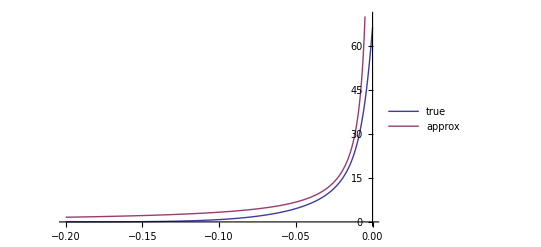

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.1;

total=U NIntegrate[fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],{m,-∞,0}];

Show[
Plot[(U fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]])/total,{m,-0.2,0},PerformanceGoal->"Speed",PlotRange->{0,All}],
Plot[{,-1/(2 (-1+√(1-m/mmax)) √(1-m/mmax) mmax Log[(1-√(1+(√(U √(mmax λ)))/(mmax π^(1/4))))/(1-√(1-mwt/mmax))])},{m,-0.2,0},PlotRange->{0,70},PlotLegends->{"true","approx"}]
]

Clear[mmax,λ,Es,n,U,mwt]
```

and for large ρmax we have

```mathematica
verylargeρapprox=-(32 ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)))/(√π ρmax^(3/2) ψwt^3);
Integrate[verylargeρapprox,{ψ,-∞,0},Assumptions->{ρmax>0,ψwt<0}];
verylargeρapprox/%
Simplify[D[2(1-√(1-m/mmax)),m]%/.a->2(1-√(1-mwt/mmax))/.b-> 2(1- √(1+mstar/mmax))/.mstar->√(Λ0approx/2)/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax)),{m<0,mwt<0,mmax>0,λ>0}]
```

(ⅇ^(-1/4 ρmax (ψ^2+(ψ-ψwt)^2)+(ρmax ψwt^2)/8) √(2/π) √ρmax)/Erfc[(√ρmax ψwt)/(2 √2)]

(ⅇ^((4 m-6 mmax+4 √(mmax (-m+mmax))-2 √(mmax (mmax-mwt))+4 √((-m+mmax) (mmax-mwt))+mwt)/(2 λ)) √(2/π))/(√((-m+mmax) λ) Erfc[((1-√(1-mwt/mmax)) √(mmax/λ))/(√2)])

compare distribution of subcriticals

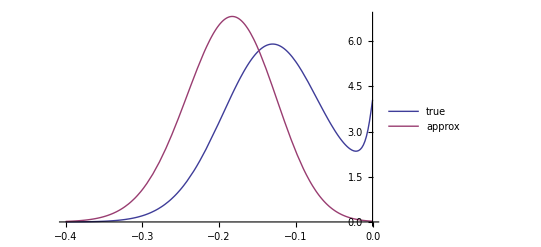

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.4;

total=U NIntegrate[fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],{m,-∞,0}];

Show[
Plot[(U fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]])/total,{m,-0.4,0},PerformanceGoal->"Speed",PlotRange->{0,All}],
Plot[{,1/(√(1-m/mmax) mmax)(ⅇ^((4 m+mwt+mmax (-6+4 √(1-m/mmax)-2 √(1-mwt/mmax)+4 √(1-m/mmax) √(1-mwt/mmax)))/(2 λ)) √(2/π) √(mmax/λ))/Erfc[((1-√(1-mwt/mmax)) √(mmax/λ))/(√2)]},{m,-0.4,0},PlotRange->{0,70},PlotLegends->{"true","approx"}]
]

Clear[mmax,λ,Es,n,U,mwt]
```

Our sufficiently critical approximation is

```mathematica
fm[0,m0,mmax,λ,n] √(2 (2 U √(mmax λ))/(√π));
Integrate[%,{m,-√((U √(mmax λ))/(√π)),√((U √(mmax λ))/(√π))}];
Simplify[%%/%,{mmax>0,λ>0}]
```

π^(1/4)/(2 √U (mmax λ)^(1/4))

compare distributions of criticals

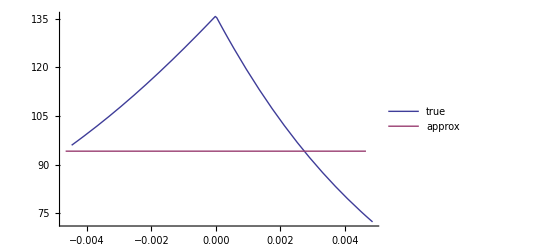

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

(*{mneg=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,-0.1}],mpos=FindRoot[2 m^2-Λ1[m,mmax,λ,n,U],{m,0.1}]};
pr0=√(Λ1[0,mmax,λ,n,U]/2);
total=U NIntegrate[fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],{m,m/.mneg,m/.mpos}];
*)
Show[
Plot[(U fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]])/total,{m,m/.mneg,m/.mpos},PerformanceGoal->"Speed",PlotRange->{0,All}],
Plot[{,π^(1/4)/(2 √U (mmax λ)^(1/4))},{m,-pr0,pr0},PlotRange->{0,All},PlotLegends->{"true","approx"}],
PlotRange->All
]

Clear[mmax,λ,Es,n,U,mwt]
```

And finally our distribution of supercriticals

```mathematica
smallψapprox=(2 ⅇ^(-(ρmax ψwt^2)/4))/(√π √ρmax ψ);
Integrate[smallψapprox,{ψ,a,b},Assumptions->{0<a<b}];
smallψapprox/%
D[2(1-√(1-m/mmax)),m]%/.a->2( 1- √(1-mstar/mmax))/.b->(√2)/(√ρmax)/.mstar->√(Λ0approx/2)/.ρmax->mmax/λ/.θ->n/2/.ψwt->2(1-√(1-mwt/mmax))/.ψ->2(1-√(1-m/mmax))
```

Note this is good only to

```mathematica
Solve[(√2)/(√ρmax)==2(1-√(1-m/mmax)),m]/.ρmax->mmax/λ//Simplify
```

{{m→(-1/2+√2 √(mmax/λ)) λ}}

Compare distn of supercriticals

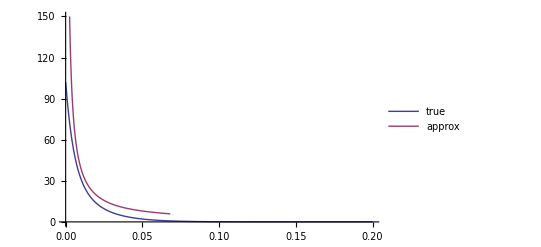

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

total=U NIntegrate[fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]],{m,0,mmax}];

Show[
Plot[(U fm[m,mwt,mmax,λ,n](1-pest[m])prescuem[m,Λ1[m,mmax,λ,n,U]])/total,{m,0,0.2},PerformanceGoal->"Speed",PlotRange->{0,All}],
Plot[{,1/(2 (1-√(1-m/mmax)) √(1-m/mmax) mmax Log[1/(√2 √(mmax/λ) (1-√(1-(√(U √(mmax λ)))/(mmax π^(1/4)))))])},{m,0,(-1/2+√2 √(mmax/λ)) λ},PlotRange->{0,150},PlotLegends->{"true","approx"}]
]

Clear[mmax,λ,Es,n,U,mwt]
```

### Plot growth rates of rescue intermediates

#### As function of wildtype growth rate (figure 7)

```mathematica
xmin=-0.3;
xmax=0.15;
ymax=30;
```

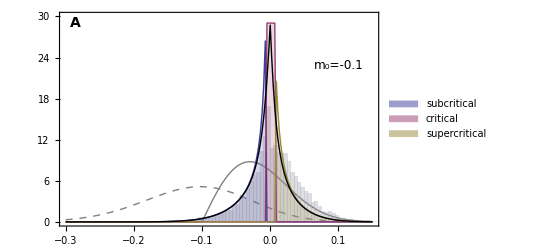

```mathematica
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.1;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[m1,mmax,λ,n,U]/2);

exact=fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]];

critical=fm[0,mwt,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U])HeavisideTheta[(m1+pr0)(pr0-m1)];

subcritical=fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-m1-pr0)];
supercritical=fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(m1-pr0)];

allexact=NIntegrate[exact,{m1,mwt,0.1}];

{
fm[m1,mwt,mmax,λ,n],
(fm[m1,mwt,mmax,λ,n]pest[m1-mwt]HeavisideTheta[m1-mwt])/NIntegrate[fm[m1,mwt,mmax,λ,n]pest[m1-mwt],{m1,mwt,mmax}]
};
oldtheory=Plot[
%,
{m1,xmin,xmax},
PlotRange->{0,All},
(*Filling->Bottom,*)
PlotStyle->{Directive[Gray,Thick,Dashed],Directive[Gray,Thick]},
PerformanceGoal->"Speed",
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"random","established"}],Scaled@{1/8,1.25/2}]
];

{subcritical/allexact,critical/allexact,supercritical/allexact};
theory=Plot[
%,
{m1,xmin,xmax},
PlotRange->{0,All},
Filling->Bottom,
PerformanceGoal->"Speed",
PlotLegends->Placed[SwatchLegend[{Directive[defaultcolors[[1]],Opacity[0.5]],Directive[defaultcolors[[2]],Opacity[0.5]],Directive[defaultcolors[[3]],Opacity[0.5]]},Style[#,12,FontFamily->"Helvetica"]&/@{"subcritical","critical","supercritical"}],Scaled@{1/8,0.65/2}]
];

exactplot=Plot[
exact/allexact,{m1,xmin,xmax},PlotStyle->Directive[Thick,Black],PerformanceGoal->"Speed",PlotRange->All,
PlotLegends->Placed[LineLegend[Style[#,12,FontFamily->"Helvetica"]&/@{"first-step"}],Scaled@{1/8,1.25/2}]
];

dat=Import[datadir<>"int_dfe_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mwt-0.10_mutmax10_nreps100000.csv"];
Select[dat,#[[2]]==2&][[All,3]];
data=Histogram[%,50,"PDF",AxesOrigin->{0,0},ChartStyle->Directive[Gray,Opacity[0.25]]];

Show[
oldtheory,data,theory,exactplot,
Frame->{True,False,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
PlotRange->{{xmin,xmax},{0,ymax}},
LabelStyle->labelstyle,
Epilog->{Text[Style["m_0="<>ToString[mwt],12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],Text[Style["A",14,Bold],Scaled@{0.05,0.95}]}
]

(*Export[imagedir<>"firststep_smallm0_regimes.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

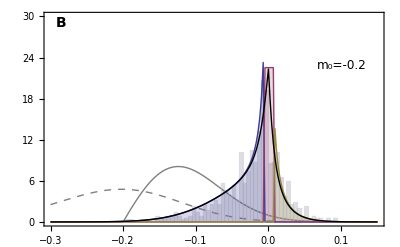

```mathematica
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[m1,mmax,λ,n,U]/2);

exact=fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]];

critical=fm[0,mwt,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U])HeavisideTheta[(m1+pr0)(pr0-m1)];

subcritical=fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-m1-pr0)];
supercritical=fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(m1-pr0)];

allexact=NIntegrate[exact,{m1,mwt,0.1}];

{
fm[m1,mwt,mmax,λ,n],
(fm[m1,mwt,mmax,λ,n]pest[m1-mwt]HeavisideTheta[m1-mwt])/NIntegrate[fm[m1,mwt,mmax,λ,n]pest[m1-mwt],{m1,mwt,mmax}]
};
oldtheory=Plot[
%,
{m1,xmin,xmax},
PlotRange->{0,All},
(*Filling->Bottom,*)
PlotStyle->{Directive[Gray,Thick,Dashed],Directive[Gray,Thick]},
PerformanceGoal->"Speed"
];

{subcritical/allexact,critical/allexact,supercritical/allexact};
theory=Plot[
%,
{m1,xmin,xmax},
PlotRange->{0,All},
Filling->Bottom,
PerformanceGoal->"Speed"
];

exactplot=Plot[
exact/allexact,{m1,xmin,xmax},PlotStyle->Directive[Thick,Black],PerformanceGoal->"Speed",PlotRange->All
];

dat=Import[datadir<>"int_dfe_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mwt-0.20_mutmax10_nreps100000.csv"];
Select[dat,#[[2]]==2&][[All,3]];
data=Histogram[%,50,"PDF",AxesOrigin->{0,0},ChartStyle->Directive[Gray,Opacity[0.25]]];

Show[
oldtheory,data,theory,exactplot,
Frame->{True,False,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
PlotRange->{{xmin,xmax},{0,ymax}},
LabelStyle->labelstyle,
Epilog->{Text[Style["m_0="<>ToString[mwt],12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],Text[Style["B",14,Bold],Scaled@{0.05,0.95}]}
]

(*Export[imagedir<>"firststep_medm0_regimes.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

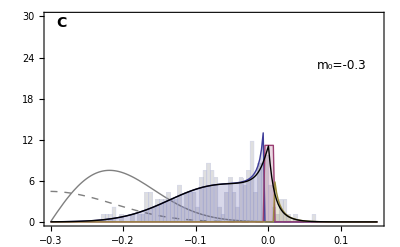

```mathematica
U=2*10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.3;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[m1,mmax,λ,n,U]/2);

exact=fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]];

critical=fm[0,mwt,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U])HeavisideTheta[(m1+pr0)(pr0-m1)];

subcritical=fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-m1-pr0)];
supercritical=fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(m1-pr0)];

allexact=NIntegrate[exact,{m1,mwt,0.1}];

{
fm[m1,mwt,mmax,λ,n],
(fm[m1,mwt,mmax,λ,n]pest[m1-mwt]HeavisideTheta[m1-mwt])/NIntegrate[fm[m1,mwt,mmax,λ,n]pest[m1-mwt],{m1,mwt,mmax}]
};
oldtheory=Plot[
%,
{m1,xmin,xmax},
PlotRange->{0,All},
(*Filling->Bottom,*)
PlotStyle->{Directive[Gray,Thick,Dashed],Directive[Gray,Thick]},
PerformanceGoal->"Speed"
];

{subcritical/allexact,critical/allexact,supercritical/allexact};
theory=Plot[
%,
{m1,xmin,xmax},
PlotRange->{0,All},
Filling->Bottom,
PerformanceGoal->"Speed"
];

exactplot=Plot[
exact/allexact,{m1,xmin,xmax},PlotStyle->Directive[Thick,Black],PerformanceGoal->"Speed",PlotRange->All
];

dat=Import[datadir<>"int_dfe_poisson_N10000_n4_U0.00200_Es0.01_mmax0.50_mwt-0.30_mutmax10_nreps1000000.csv"];
Select[dat,#[[2]]==2&][[All,3]];
data=Histogram[%,50,"PDF",AxesOrigin->{0,0},ChartStyle->Directive[Gray,Opacity[0.25]]];

Show[
oldtheory,data,theory,exactplot,
Frame->{True,False,False,False},
FrameLabel->{"Growth rate"},
PlotRange->{{xmin,xmax},{0,ymax}},
LabelStyle->labelstyle,
Epilog->{Text[Style["m_0="<>ToString[mwt],12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],Text[Style["C",14,Bold],Scaled@{0.05,0.95}]}
]

(*Export[imagedir<>"firststep_largem0_regimes.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

```mathematica
Clear[ymax,xmin,xmax]
```

#### As function of mutation (figure S2)

```mathematica
xmin=mwt;
xmax=-mwt/2;
ymax=70;
```

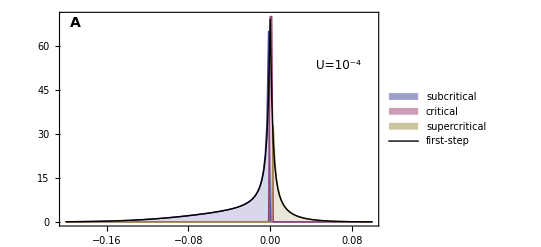

```mathematica
U=10^-4;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;


{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[m1,mmax,λ,n,U]/2);

exact=fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]];

critical=fm[0,mwt,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U])HeavisideTheta[(m1+pr0)(pr0-m1)];

subcritical=fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-m1-pr0)];
supercritical=fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(m1-pr0)];
total=NIntegrate[exact,{m1,mwt,0.1}];

Show[
Plot[
{subcritical/total,critical/total,supercritical/total},
{m1,xmin,xmax},
PlotRange->{0,All},
(*PlotStyle->Thick,*)
Filling->Bottom,
Frame->{True,False,False,False},
PlotLegends->
Placed[SwatchLegend[{Directive[defaultcolors[[1]],Opacity[0.5]],Directive[defaultcolors[[2]],Opacity[0.5]],Directive[defaultcolors[[3]],Opacity[0.5]]},Style[#,12,FontFamily->"Helvetica"]&/@{"subcritical","critical","supercritical"}],Scaled@{1/8,0.5}],
LabelStyle->labelstyle,
Epilog->{Text[Style["U=10^-4",12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],Text[Style["A",14,Bold],Scaled@{0.05,0.95}]},
PerformanceGoal->"Speed"
],
Plot[exact/total,{m1,xmin,xmax},PlotStyle->Directive[Thick,Black],PerformanceGoal->"Speed",PlotRange->All,
PlotLegends->Placed[Style[#,12,FontFamily->"Helvetica"]&/@{"first-step"},Scaled@{1/8,0.7}]
],
PlotRange->{{xmin,xmax},{0,ymax}}
]

(*Export[imagedir<>"firststep_smallU.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

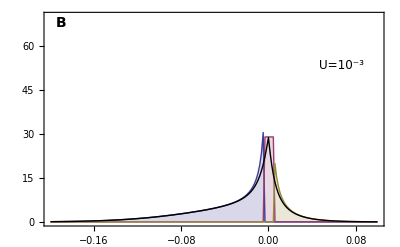

```mathematica
U=10^-3;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[m1,mmax,λ,n,U]/2);

exact=fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]];

critical=fm[0,mwt,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U])HeavisideTheta[(m1+pr0)(pr0-m1)];

subcritical=fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-m1-pr0)];
supercritical=fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(m1-pr0)];

total=NIntegrate[exact,{m1,mwt,0.1}];

Show[
Plot[
{subcritical/total,critical/total,supercritical/total},
{m1,xmin,xmax},
PlotRange->{0,All},
(*PlotStyle->Thick,*)
Filling->Bottom,
Frame->{True,False,False,False},
LabelStyle->labelstyle,
Epilog->{Text[Style["U=10^-3",12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],Text[Style["B",14,Bold],Scaled@{0.05,0.95}]},
PerformanceGoal->"Speed"
],
Plot[{exact/total},{m1,xmin,xmax},PlotStyle->Directive[Thick,Black],PerformanceGoal->"Speed",PlotRange->All(*,Filling->Bottom*)],
PlotRange->{{xmin,xmax},{0,ymax}}
]

(*Export[imagedir<>"firststep_medU.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

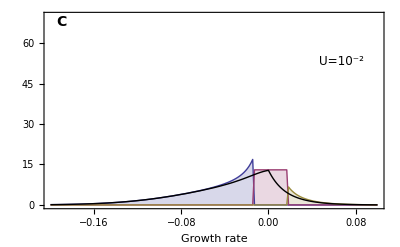

```mathematica
U=10^-2;
mmax=0.5;
λ=2Es/n;
Es=0.01;
n=4;
mwt=-0.2;

{mneg=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,-0.1}],mpos=FindRoot[2 m1^2-Λ1[m1,mmax,λ,n,U],{m1,0.1}]};
pr0=√(Λ1[m1,mmax,λ,n,U]/2);

exact=fm[m1,mwt,mmax,λ,n](1-pest[m1])prescuem[m1,Λ1[m1,mmax,λ,n,U]];

critical=fm[0,mwt,mmax,λ,n] √(2Λ1[0,mmax,λ,n,U])HeavisideTheta[(m1+pr0)(pr0-m1)];

subcritical=fm[m1,mwt,mmax,λ,n] Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(-m1-pr0)];
supercritical=fm[m1,mwt,mmax,λ,n](1-pest[m1])Λ1[m1,mmax,λ,n,U]/Abs[m1] HeavisideTheta[(m1-pr0)];
total=NIntegrate[exact,{m1,mwt,0.1}];

Show[
Plot[
{subcritical/total,critical/total,supercritical/total},
{m1,xmin,xmax},
PlotRange->{0,All},
Filling->Bottom,
Frame->{True,False,False,False},
FrameLabel->{"Growth rate",""},
LabelStyle->labelstyle,
Epilog->{Text[Style["U=10^-2",12,FontFamily->"Helvetica"],Scaled@{7/8,3/4}],Text[Style["C",14,Bold],Scaled@{0.05,0.95}]},
PerformanceGoal->"Speed"
],
Plot[{exact/total},{m1,xmin,xmax},PlotStyle->Directive[Thick,Black],PerformanceGoal->"Speed",PlotRange->All],
PlotRange->{{xmin,xmax},{0,ymax}}
]

(*Export[imagedir<>"firststep_largeU.pdf",%];*)

Clear[mmax,λ,Es,n,U,mwt]
```

```mathematica
Clear[ymax,xmin,xmax]
```